```mathematica
(* Mathematica code for Model1 of Eshra et al. eLife 2021 *)
(* Stefan Hallermann and Hartmut Schmidt Aug 2021 *)
```

# Import

## general

```mathematica
(* all Ca in uM, all times in ms, all ampltiudes and Nv in vesicels *)
```

```mathematica
CmToVesConversionFactor = (1/90.12)*(1/70*^-18);(* explained in methods *)
```

```mathematica
rrp=10;(* pool of release-ready vesicles per connection *)
```

```mathematica
dir=NotebookDirectory[];
SetDirectory[dir]; 
dataFolder="../data to fit/";
```

## tau1 Cm 5kHz

```mathematica
data=Import[dataFolder<>"all_t1_v02_C5.txt","Table"];
```

```mathematica
dataT1C5Ca=0.001*data[[All,1]];
dataT1C5RelRate=1000.*data[[All,2]];
dataT1C5Delay=data[[All,3]];
dataT1C5ChiRatio= data[[All,4]];
dataT1C5Amplitude=CmToVesConversionFactor data[[All,5]];

dataT1C5Nv=Table[0,{7}];
tmp1=1;tmp2=6;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C5Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
```

## tau1 Cm 10kHz

```mathematica
data=Import[dataFolder<>"all_t1_v02_C10.txt","Table"];
```

```mathematica
dataT1C10Ca=0.001*data[[All,1]];
dataT1C10RelRate=1000.*data[[All,2]];
dataT1C10Delay=data[[All,3]];
dataT1C10ChiRatio= data[[All,4]];
dataT1C10Amplitude=CmToVesConversionFactor data[[All,5]];

dataT1C10Nv=Table[0,{7}];
tmp1=1;tmp2=6;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1C10Nv[[tmp1]]=CmToVesConversionFactor data[[All,tmp2]];
```

## tau1 Deconv

```mathematica
data=Import[dataFolder<>"all_t1_v02_D.txt","Table"];
```

```mathematica
dataT1DCa=0.001*data[[All,1]];
dataT1DRelRate=1000.*data[[All,2]];
dataT1DDelay=data[[All,3]];
dataT1DChiRatio= data[[All,4]];
dataT1DAmplitude= data[[All,5]];

dataT1DNv=Table[0,{7}];
tmp1=1;tmp2=6;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
tmp1+=1;tmp2+=1;dataT1DNv[[tmp1]]=data[[All,tmp2]];
```

## tau2 Cm 5kHz

```mathematica
data=Import[dataFolder<>"all_t2_v02_C5.txt","Table"];
```

```mathematica
dataT2C5Ca=0.001*data[[All,1]];
dataT2C5RelRate=1000.*data[[All,2]];
dataT2C5Amplitude2=CmToVesConversionFactor data[[All,3]];
dataT2C5Amplitude1=CmToVesConversionFactor data[[All,4]];
```

## tau2 Cm 10kHz

```mathematica
data=Import[dataFolder<>"all_t2_v02_C10.txt","Table"];
```

```mathematica
dataT2C10Ca=0.001*data[[All,1]];
dataT2C10RelRate=1000.*data[[All,2]];
dataT2C10Amplitude2=CmToVesConversionFactor data[[All,3]];dataT2C10Amplitude1=CmToVesConversionFactor data[[All,4]];
```

## tau2 Deconv

```mathematica
data=Import[dataFolder<>"all_t2_v02_D.txt","Table"];
```

```mathematica
dataT2DCa=0.001*data[[All,1]];
dataT2DRelRate=1000.*data[[All,2]];
dataT2DAmplitude2= data[[All,3]];
dataT2DAmplitude1= data[[All,4]];
```

## local Ca

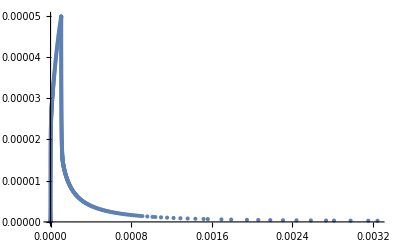

```mathematica
data=Import[dataFolder<>"local Ca at 20 nm in uM and ms.txt","Table"];
dataLocalCa=1*^-6 data[[All,1]];
dataLocalCaTime=1*^-3 data[[All,2]];
ListPlot[Transpose[{dataLocalCaTime,dataLocalCa}],PlotRange->All]
```

# General parameters and definitions

## general stuff

```mathematica
(* for calulations: time in s, Ca in M *)
numberOfFitParamToBeSaved=16;
(*
1 max release

Mono
2 chi2Mono
3 delayMono
4 ampMono
5 1/tau1Mono

Bi
6 chi2Mono/chi2Bi
7 delay
8 amp
9 amp1 (=amp*relative amp1)
10 1/tau1
11 1/tau2

merge
12 delay
13 amp
14 amp1
15 1/tau1
16 1/tau2
*)
cursorStart=-0.002;(*s*)
cursorEnd=0.01;(*s*)
cursorEndLong=0.061;(*s*)
timeOfNv={0.0001,0.0002,0.001,0.005,0.01,0.1,0.4};
SeedRandom[1];
myMaxIterations=100;
```

```mathematica
timeStart=AbsoluteTime[]
```

3.839313629403805×10^9

## noiseRepeats

```mathematica
noiseRepeats=3;
(* should be increased to 50 for a full dataset *)
myQuantile1=0.25;
myQuantile2=0.75;
```

## export parameters

```mathematica
dtOfPlotsForExport=20*^-5;
exportYes=1;
```

## sampling and myNoise

```mathematica
samplingOfDataInKHzC5=5;
myNoiseC5=0.1;(*cannot be 0*)
signalToNoiseRatioC5=1.;(*minimum s-to-n-ratio to attempt fitting*)
dtOfDataC5=(1/(1000*samplingOfDataInKHzC5));

samplingOfDataInKHzC10=10;
myNoiseC10=0.1;(*cannot be 0*)
signalToNoiseRatioC10=1.;(*minimum s-to-n-ratio to attempt fitting*)
dtOfDataC10=(1/(1000*samplingOfDataInKHzC10));

samplingOfDataInKHzD=10;
myNoiseD=0.02;(*cannot be 0*)
signalToNoiseRatioD=1.;(*minimum s-to-n-ratio to attempt fitting*)
dtOfDataD=(1/(1000*samplingOfDataInKHzD));

samplingOfDataInKHzLong=1;
myNoiseLong=0.1;(*cannot be 0*)
dtOfDataLong=(1/(1000*samplingOfDataInKHzLong));
```

## number of simulations per DMN

```mathematica
aNumberDMN05=2;
aNumberDMN2=2;
aNumberDMN10=2;

(* for full dataset: *)
(*
aNumberDMN05=2*20;
aNumberDMN2=2*17;
aNumberDMN10=2*10;
*)
```

## Exp fit function

```mathematica
myFitMono[t_]:=If[t<=delayMono,0,ampMono (1- Exp[-(t-delayMono)/tau1Mono])];

myFitBi[t_]:=If[t<=delay,0,amp (1- amp1 Exp[-(t-delay)/tau1]-(1-amp1) Exp[-(t-delay)/tau2])];

(*guess for 10 uM; will be changed according to a power of 1 law*)(*in s*)
ampGuess=2.;(*each pool has size 1.0*)
tau1Guess=0.001;(*in s*)
delayGuess=0.0005;(*in s*)
amp1Guess=0.5;
```

# Calculate Ca transients

#### Concentrations in mol/l; DMn uncaging according to Faas et al., 2005, 2007 First, the resting conditions are numerically calculated. Subsequently, the resulting values are used as initial conditions for the main simulations of the flash-evoked Ca2+ transitions . All calculations are repeated in a loop with increasing uncaging efficacy for three different DMN concentrations. The resulting free Ca2+ concentration is later used to drive the release schemes.

## General definitions for all DMN conc.

```mathematica
CaListReal=CaListDye={};
```

## 0.5 mM DMN

## general parameters

```mathematica
TimeWindow=0.006; (*End of simulation*)
tflash=0.0;   (*Time of flash*)
PlStart=0.; (*Plot start*)

af=0.67; (*fast uncaging fraction; Faas et al*)

(*Select dye*)
OGB1=0;
OGB5N=0;
OGB6F=0;
Fluo5F=1;

CaRest=227.*10^-9; (*Free pre-flash rersting Ca; equilibrates with all buffers and DM*)
MgT=0.5*10^-3; (*total Mg in pipette*)
γ=0.;  (*Pump rate*)

(*Concentrations of dye, buffers, DM*)
OGtotal =50.*10^-6 ;
ATPtotal =5.*10^-3 ;
MBtotal =480.*10^-6 ;(*(*Delvendahl, PNAS, 2015*)*)   

DMT = 0.5*10^-3;    (*total concentration of DMn *)
(*uncaging efficiency*)
aStartDMN05=0.08;
aEndDMN05=0.5;
```

## definitions and loop

```mathematica
(*Dye*)
If[OGB1==1,
kOnOG  = 4.3*10^8;
kOffOG = 103.;]

If[OGB5N==1,
kOnOG  = 2.5*10^8;
kOffOG = 6000.;]

If[OGB6F==1,
kOnOG  = 3.*10^8;
kOffOG = 900.;]

If[Fluo5F==1,
kOnOG  = 3.*10^8;
kOffOG = 249.;] (*Delvendahl PNAS; before: 432*)

KdOG = kOffOG/kOnOG;
kappaOG=OGtotal/KdOG;

(*ATP*)
kOnATP  = 5.*10^8;
kOffATP = 100000.;
kOnMgATP  = 1.*10^7; (*Bollmann Dissertation S. 59; *)
kOffMgATP = 1000.;

KdATP = kOffATP/kOnATP;
kappaATP=ATPtotal/KdATP;
KdMgATP = kOffMgATP/kOnMgATP;

(*DM*)
If[MgT==0.,
kOnDM=1.98*10^7;(*Faas Plos Biol, 2007*)
kOffDM = 0.14;  
,
kOnDM=2.9*10^7;(*Faas Biophys J, 2005*)
kOffDM = 0.19;
]

(*Mg binding constants for DMn, DMf, DMs*)
kOnMg=1.3*10^5;  (*all values for Mg are from Faas et al., 2005*)
kOffMg=0.2;

(*Ca binding constants for PP*)
kOnPP2=kOnPP1=kOnDM;
kOffPP2=3.6*10^3;
If[MgT==0.,
kOffPP1=7.*10^4;,
kOffPP1=6.9*10^4;  ]

(*Mg binding constants for PP1,PP2*)
kOffMgPP=3.*10^2; (*for PP1,PP2*)
konMgPP=kOnMg; (*koMgPP not used in below diff. eq., only kOnMg*)

(*Equilibrium constants (not complete)*)
KdDM = kOffDM/kOnDM;
KdPP1=kOffPP1/kOnPP1;
KdMg = kOffMg/kOnMg;
kappaDM=DMT/KdDM;

 (*Endogenous buffer*)
kOnMB  = 5*10^8;(*Delvendahl, PNAS, 2015*)
kOffMB =16000;
KdMB = kOffMB/kOnMB;

TRest=1000.;


(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)


For[aCount=1,aCount≤ aNumberDMN05,aCount+=1,
a=10^(Log10[aStartDMN05]+(aCount-1)*(Log10[aEndDMN05]-Log10[aStartDMN05])/(aNumberDMN05-1));

(*------------------------- Resting Equations -------------------------------------------*)

(*Dye*)
OGRest:={

OG[0]==OGtotal,
CaOG[0]==0,

OG'[tt]==-kOnOG*CaRest* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*CaRest* OG[tt]- kOffOG *CaOG[tt]
}
;

(*ATP*)
ATPRest:={

ATP[0]==ATPtotal,
CaATP[0]==0,
MgATP[0]==0,

ATP'[tt]==-kOnATP*CaRest* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*CaRest* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]

}

;

(*DM nitrophene*)
DMnRest:={

DMn[0]==(1-a)*DMT,
CaDMn[0]==0.,
MgDMn[0]==0.,

DMn'[tt]==-kOnDM*CaRest* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*CaRest* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}

;
DMfRest:={

DMf[0]==a*af*DMT,
CaDMf[0]==0.,
MgDMf[0]==0.,

DMf'[tt]==-kOnDM*CaRest* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt],
CaDMf'[tt]==kOnDM*CaRest* DMf[tt]- kOffDM *CaDMf[tt],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]
}

;
DMsRest:={

DMs[0]==a*(1-af)*DMT,
CaDMs[0]==0.,
MgDMs[0]==0.,

DMs'[tt]==-kOnDM*CaRest* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt],
CaDMs'[tt]==kOnDM*CaRest* DMs[tt]- kOffDM *CaDMs[tt],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]
}
;

(*Endogeneous buffer*)
MBRest:={

MB[0]==MBtotal,
CaMB[0]==0,

MB'[tt]==-kOnMB*CaRest* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*CaRest*MB[tt]- kOffMB *CaMB[tt]
}

;

(*Free Mg*)
MgfRest:={
Mg[0]==MgT,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
}

;
EqRest:={ATPRest,MgfRest,OGRest,DMnRest,DMfRest,DMsRest,MBRest};
VarsRest:={ATP,Mg,CaATP,MgATP,CaOG,OG,DMn,CaDMn,MgDMn,DMf,CaDMf,MgDMf,DMs,CaDMs,MgDMs,MB,CaMB}
;
solr:=NDSolve[EqRest,VarsRest,{tt,0,TRest}]
;

Ca0 =CaRest;
Mg0 = Extract[Mg[TRest]/.solr,1];
ATP0 = Extract[ATP[TRest]/.solr,1];
CaATP0=Extract[CaATP[TRest]/.solr,1];
MgATP0=Extract[MgATP[TRest]/.solr,1];
OG0 = Extract[OG[TRest]/.solr,1];
CaOG0 = Extract[CaOG[TRest]/.solr,1];
DMn0= Extract[DMn[TRest]/.solr,1];
CaDMn0= Extract[CaDMn[TRest]/.solr,1];
MgDMn0= Extract[MgDMn[TRest]/.solr,1];
DMf0= Extract[DMf[TRest]/.solr,1];
CaDMf0= Extract[CaDMf[TRest]/.solr,1];
MgDMf0= Extract[MgDMf[TRest]/.solr,1];
DMs0= Extract[DMs[TRest]/.solr,1];
CaDMs0= Extract[CaDMs[TRest]/.solr,1];
MgDMs0= Extract[MgDMs[TRest]/.solr,1];
MB0 = Extract[MB[TRest]/.solr,1];
CaMB0 = Extract[CaMB[TRest]/.solr,1];


ClearAll[EqRest,VarsRest];


(*------------------------- Flash Equations -------------------------------------------*)

(*Dye*)
BufferOG:={

OG[0]==OG0,
CaOG[0]==CaOG0,

OG'[tt]==-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*Ca[tt]* OG[tt]- kOffOG *CaOG[tt]}
;

(*ATP*)
BufferATP:={

ATP[0]==ATP0,
CaATP[0]==CaATP0,
MgATP[0]==MgATP0,

ATP'[tt]==-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*Ca[tt]* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]
}
;

(*fast (tauf) and slow (taus) time constants for uncageing; Faas et al., 2005,2007*)
If[MgT==0.,
tauf=15.2*10^-6;  (*Faas, 2007*)
taus=1.9*10^-3;  
,
tauf=15.*10^-6;  (*Faas,2005*)
taus=2.*10^-3;  ]

;

(*The differential equations*)
(*non uncaging fraction of DMn*)
BufferDMn:={

DMn[0]==DMn0,
CaDMn[0]==CaDMn0,
MgDMn[0]==MgDMn0,

DMn'[tt]==-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*Ca[tt]* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}
;

(*fast uncaging fraction of DMn*)
BufferDMf:={

DMf[0]==DMf0,
CaDMf[0]==CaDMf0,
MgDMf[0]==MgDMf0,

DMf'[tt]==-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]-1/tauf*DMf[tt]*UnitStep[tt-tflash],
CaDMf'[tt]==kOnDM*Ca[tt]* DMf[tt]- kOffDM *CaDMf[tt]-1/tauf*CaDMf[tt]*UnitStep[tt-tflash],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]-1/tauf*MgDMf[tt]*UnitStep[tt-tflash]
}

;
(*slow uncaging fraction of DMn*)
BufferDMs:={

DMs[0]==DMs0,
CaDMs[0]==CaDMs0,
MgDMs[0]==MgDMs0,

DMs'[tt]==-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]-1/taus*DMs[tt]*UnitStep[tt-tflash],
CaDMs'[tt]==kOnDM*Ca[tt]* DMs[tt]- kOffDM *CaDMs[tt]-1/taus*CaDMs[tt]*UnitStep[tt-tflash],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]-1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*Photoproducts*)
(*PP2: comes from DMf,DMs and MgDMf,MgDMs; but also binds Ca*)
BufferPP2:={

PP2[0]==0,
CaPP2[0]==0,
MgPP2[0]==0,

PP2'[tt]==-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]+2*(1/tauf*DMf[tt]*UnitStep[tt-tflash]+1/taus*DMs[tt]*UnitStep[tt-tflash])
+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash],

CaPP2'[tt]==kOnPP2*Ca[tt]* PP2[tt]- kOffPP2*CaPP2[tt],

MgPP2'[tt]==kOnMg*Mg[tt]* PP2[tt]- kOffMgPP*MgPP2[tt]+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*PP1: Comes from CaDMf,CaDMs and binds Ca and Mg*)
BufferPP1:={

PP1[0]==0,
CaPP1[0]==0,
MgPP1[0]==0,

PP1'[tt]==-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

CaPP1'[tt]==kOnPP1*Ca[tt]* PP1[tt]- kOffPP1 *CaPP1[tt]+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

MgPP1'[tt]==kOnMg*Mg[tt]* PP1[tt]- kOffMgPP*MgPP1[tt]

}
;

(*Endogeneous Buffer*)
BufferMB:={

MB[0]==MB0,
CaMB[0]==CaMB0,

MB'[tt]==-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*Ca[tt]*MB[tt]- kOffMB *CaMB[tt]}

;

(*Clear[Eqns,Vars,sol]*)

(*Free Ca*)
FreeCa:= {
Ca[0]==Ca0,

Ca'[tt]== -γ *(Ca[tt]-CaRest)
(*DMn*)
-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]
-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]
-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]
-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]
-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]
(*buffers*)
-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]
-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt]
(*dye*)
-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt]
 }
;

(*Free Mg*)
FreeMg:={
Mg[0]==Mg0,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]
-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
}

;

Eqns:={BufferDMn,BufferDMf,BufferDMs,BufferATP,BufferPP1,BufferPP2,FreeCa,FreeMg,BufferMB,BufferOG}
;
Vars:={ATP,CaATP,MgATP,Ca,Mg,CaDMn,DMn,CaDMf,DMf,CaDMs,DMs,CaPP1,PP1,CaPP2,PP2,MgPP2,MgPP1,MB,CaMB,OG,CaOG}
;
sol := NDSolve[Eqns,Vars,{tt,0.,TimeWindow}(*,Method->{"EquationSimplification"->"Solve"}*)]
;
CafP=Extract[Ca[TimeWindow]/.sol,1];
CafOG=KdOG*CaOG[tt]/OG[tt];

AppendTo[CaListReal,Evaluate[{Ca[tt]}/.sol]];
AppendTo[CaListDye,Evaluate[{CafOG}/.sol]];

];
```

## 2 mM DMN

## general parameters

```mathematica
TimeWindow=0.006; (*End of simulation*)
tflash=0.0;   (*Time of flash*)
PlStart=0.; (*Plot start*)

af=0.67; (*fast uncaging fraction; Faas et al*)

(*Select dye*)
OGB1=0;
OGB5N=1;
OGB6F=0;
Fluo5F=0;

CaRest=227.*10^-9; (*Free pre-flash rersting Ca; equilibrates with all buffers and DM*)
MgT=0.5*10^-3; (*total Mg in pipette*)
γ=0.;  (*Pump rate*)

(*Concentrations of dye, buffers, DM*)
OGtotal =200.*10^-6 ;
ATPtotal =5.*10^-3 ;
MBtotal =480.*10^-6 ;(*(*Delvendahl, PNAS, 2015*)*)   

DMT = 2.*10^-3;    (*total concentration of DMn *)
(*uncaging efficiency*)
aStartDMN2=0.15;
aEndDMN2=0.55;
```

## definitions and loop

```mathematica
(*Dye*)
If[OGB1==1,
kOnOG  = 4.3*10^8;
kOffOG = 103.;]

If[OGB5N==1,
kOnOG  = 2.5*10^8;
kOffOG = 6000.;]

If[OGB6F==1,
kOnOG  = 3.*10^8;
kOffOG = 900.;]

If[Fluo5F==1,
kOnOG  = 3.*10^8;
kOffOG = 249.;] (*Delvendahl PNAS; before: 432*)

KdOG = kOffOG/kOnOG;
kappaOG=OGtotal/KdOG;

(*ATP*)
kOnATP  = 5.*10^8;
kOffATP = 100000.;
kOnMgATP  = 1.*10^7; (*Bollmann Dissertation S. 59; *)
kOffMgATP = 1000.;

KdATP = kOffATP/kOnATP;
kappaATP=ATPtotal/KdATP;
KdMgATP = kOffMgATP/kOnMgATP;

(*DM*)
If[MgT==0.,
kOnDM=1.98*10^7;(*Faas Plos Biol, 2007*)
kOffDM = 0.14;  
,
kOnDM=2.9*10^7;(*Faas Biophys J, 2005*)
kOffDM = 0.19;
]

(*Mg binding constants for DMn, DMf, DMs*)
kOnMg=1.3*10^5;  (*all values for Mg are from Faas et al., 2005*)
kOffMg=0.2;

(*Ca binding constants for PP*)
kOnPP2=kOnPP1=kOnDM;
kOffPP2=3.6*10^3;
If[MgT==0.,
kOffPP1=7.*10^4;,
kOffPP1=6.9*10^4;  ]

(*Mg binding constants for PP1,PP2*)
kOffMgPP=3.*10^2; (*for PP1,PP2*)
konMgPP=kOnMg; (*koMgPP not used in below diff. eq., only kOnMg*)

(*Equilibrium constants (not complete)*)
KdDM = kOffDM/kOnDM;
KdPP1=kOffPP1/kOnPP1;
KdMg = kOffMg/kOnMg;
kappaDM=DMT/KdDM;

 (*Endogenous buffer*)
kOnMB  = 5*10^8;(*Delvendahl, PNAS, 2015*)
kOffMB =16000;
KdMB = kOffMB/kOnMB;

TRest=1000.;


(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)

For[aCount=1,aCount≤ aNumberDMN2,aCount+=1,
a=10^(Log10[aStartDMN2]+(aCount-1)*(Log10[aEndDMN2]-Log10[aStartDMN2])/(aNumberDMN2-1));

(*------------------------- Resting Equations -------------------------------------------*)

(*Dye*)
OGRest:={

OG[0]==OGtotal,
CaOG[0]==0,

OG'[tt]==-kOnOG*CaRest* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*CaRest* OG[tt]- kOffOG *CaOG[tt]
}
;

(*ATP*)
ATPRest:={

ATP[0]==ATPtotal,
CaATP[0]==0,
MgATP[0]==0,

ATP'[tt]==-kOnATP*CaRest* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*CaRest* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]

}

;

(*DM nitrophene*)
DMnRest:={

DMn[0]==(1-a)*DMT,
CaDMn[0]==0.,
MgDMn[0]==0.,

DMn'[tt]==-kOnDM*CaRest* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*CaRest* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}

;
DMfRest:={

DMf[0]==a*af*DMT,
CaDMf[0]==0.,
MgDMf[0]==0.,

DMf'[tt]==-kOnDM*CaRest* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt],
CaDMf'[tt]==kOnDM*CaRest* DMf[tt]- kOffDM *CaDMf[tt],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]
}

;
DMsRest:={

DMs[0]==a*(1-af)*DMT,
CaDMs[0]==0.,
MgDMs[0]==0.,

DMs'[tt]==-kOnDM*CaRest* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt],
CaDMs'[tt]==kOnDM*CaRest* DMs[tt]- kOffDM *CaDMs[tt],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]
}
;

(*Endogeneous buffer*)
MBRest:={

MB[0]==MBtotal,
CaMB[0]==0,

MB'[tt]==-kOnMB*CaRest* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*CaRest*MB[tt]- kOffMB *CaMB[tt]
}

;

(*Free Mg*)
MgfRest:={
Mg[0]==MgT,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
}

;
EqRest:={ATPRest,MgfRest,OGRest,DMnRest,DMfRest,DMsRest,MBRest};
VarsRest:={ATP,Mg,CaATP,MgATP,CaOG,OG,DMn,CaDMn,MgDMn,DMf,CaDMf,MgDMf,DMs,CaDMs,MgDMs,MB,CaMB}
;
solr:=NDSolve[EqRest,VarsRest,{tt,0,TRest}]
;

Ca0 =CaRest;
Mg0 = Extract[Mg[TRest]/.solr,1];
ATP0 = Extract[ATP[TRest]/.solr,1];
CaATP0=Extract[CaATP[TRest]/.solr,1];
MgATP0=Extract[MgATP[TRest]/.solr,1];
OG0 = Extract[OG[TRest]/.solr,1];
CaOG0 = Extract[CaOG[TRest]/.solr,1];
DMn0= Extract[DMn[TRest]/.solr,1];
CaDMn0= Extract[CaDMn[TRest]/.solr,1];
MgDMn0= Extract[MgDMn[TRest]/.solr,1];
DMf0= Extract[DMf[TRest]/.solr,1];
CaDMf0= Extract[CaDMf[TRest]/.solr,1];
MgDMf0= Extract[MgDMf[TRest]/.solr,1];
DMs0= Extract[DMs[TRest]/.solr,1];
CaDMs0= Extract[CaDMs[TRest]/.solr,1];
MgDMs0= Extract[MgDMs[TRest]/.solr,1];
MB0 = Extract[MB[TRest]/.solr,1];
CaMB0 = Extract[CaMB[TRest]/.solr,1];


ClearAll[EqRest,VarsRest];


(*------------------------- Flash Equations -------------------------------------------*)

(*Dye*)
BufferOG:={

OG[0]==OG0,
CaOG[0]==CaOG0,

OG'[tt]==-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*Ca[tt]* OG[tt]- kOffOG *CaOG[tt]}
;

(*ATP*)
BufferATP:={

ATP[0]==ATP0,
CaATP[0]==CaATP0,
MgATP[0]==MgATP0,

ATP'[tt]==-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*Ca[tt]* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]
}
;

(*fast (tauf) and slow (taus) time constants for uncageing; Faas et al., 2005,2007*)
If[MgT==0.,
tauf=15.2*10^-6;  (*Faas, 2007*)
taus=1.9*10^-3;  
,
tauf=15.*10^-6;  (*Faas,2005*)
taus=2.*10^-3;  ]

;

(*The differential equations*)
(*non uncaging fraction of DMn*)
BufferDMn:={

DMn[0]==DMn0,
CaDMn[0]==CaDMn0,
MgDMn[0]==MgDMn0,

DMn'[tt]==-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*Ca[tt]* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}
;

(*fast uncaging fraction of DMn*)
BufferDMf:={

DMf[0]==DMf0,
CaDMf[0]==CaDMf0,
MgDMf[0]==MgDMf0,

DMf'[tt]==-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]-1/tauf*DMf[tt]*UnitStep[tt-tflash],
CaDMf'[tt]==kOnDM*Ca[tt]* DMf[tt]- kOffDM *CaDMf[tt]-1/tauf*CaDMf[tt]*UnitStep[tt-tflash],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]-1/tauf*MgDMf[tt]*UnitStep[tt-tflash]
}

;
(*slow uncaging fraction of DMn*)
BufferDMs:={

DMs[0]==DMs0,
CaDMs[0]==CaDMs0,
MgDMs[0]==MgDMs0,

DMs'[tt]==-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]-1/taus*DMs[tt]*UnitStep[tt-tflash],
CaDMs'[tt]==kOnDM*Ca[tt]* DMs[tt]- kOffDM *CaDMs[tt]-1/taus*CaDMs[tt]*UnitStep[tt-tflash],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]-1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*Photoproducts*)
(*PP2: comes from DMf,DMs and MgDMf,MgDMs; but also binds Ca*)
BufferPP2:={

PP2[0]==0,
CaPP2[0]==0,
MgPP2[0]==0,

PP2'[tt]==-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]+2*(1/tauf*DMf[tt]*UnitStep[tt-tflash]+1/taus*DMs[tt]*UnitStep[tt-tflash])
+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash],

CaPP2'[tt]==kOnPP2*Ca[tt]* PP2[tt]- kOffPP2*CaPP2[tt],

MgPP2'[tt]==kOnMg*Mg[tt]* PP2[tt]- kOffMgPP*MgPP2[tt]+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*PP1: Comes from CaDMf,CaDMs and binds Ca and Mg*)
BufferPP1:={

PP1[0]==0,
CaPP1[0]==0,
MgPP1[0]==0,

PP1'[tt]==-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

CaPP1'[tt]==kOnPP1*Ca[tt]* PP1[tt]- kOffPP1 *CaPP1[tt]+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

MgPP1'[tt]==kOnMg*Mg[tt]* PP1[tt]- kOffMgPP*MgPP1[tt]

}
;

(*Endogeneous Buffer*)
BufferMB:={

MB[0]==MB0,
CaMB[0]==CaMB0,

MB'[tt]==-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*Ca[tt]*MB[tt]- kOffMB *CaMB[tt]}

;

(*Clear[Eqns,Vars,sol]*)

(*Free Ca*)
FreeCa:= {
Ca[0]==Ca0,

Ca'[tt]== -γ *(Ca[tt]-CaRest)
(*DMn*)
-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]
-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]
-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]
-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]
-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]
(*buffers*)
-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]
-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt]
(*dye*)
-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt]
 }
;

(*Free Mg*)
FreeMg:={
Mg[0]==Mg0,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]
-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
}

;

Eqns:={BufferDMn,BufferDMf,BufferDMs,BufferATP,BufferPP1,BufferPP2,FreeCa,FreeMg,BufferMB,BufferOG}
;
Vars:={ATP,CaATP,MgATP,Ca,Mg,CaDMn,DMn,CaDMf,DMf,CaDMs,DMs,CaPP1,PP1,CaPP2,PP2,MgPP2,MgPP1,MB,CaMB,OG,CaOG}
;
sol := NDSolve[Eqns,Vars,{tt,0.,TimeWindow}(*,Method->{"EquationSimplification"->"Solve"}*)]
;
CafP=Extract[Ca[TimeWindow]/.sol,1];
CafOG=KdOG*CaOG[tt]/OG[tt];

AppendTo[CaListReal,Evaluate[{Ca[tt]}/.sol]];
AppendTo[CaListDye,Evaluate[{CafOG}/.sol]];

];
```

## 10 mM DMN

## general parameters

```mathematica
TimeWindow=0.006; (*End of simulation*)
tflash=0.0;   (*Time of flash*)
PlStart=0.; (*Plot start*)

af=0.67; (*fast uncaging fraction; Faas et al*)

(*Select dye*)
OGB1=0;
OGB5N=1;
OGB6F=0;
Fluo5F=0;

CaRest=227.*10^-9; (*Free pre-flash rersting Ca; equilibrates with all buffers and DM*)
MgT=0.5*10^-3; (*total Mg in pipette*)
γ=0.;  (*Pump rate*)

(*Concentrations of dye, buffers, DM*)
OGtotal =200.*10^-6 ;
ATPtotal =5.*10^-3 ;
MBtotal =480.*10^-6 ;(*(*Delvendahl, PNAS, 2015*)*)   

DMT = 10.*10^-3;    (*total concentration of DMn *)
(*uncaging efficiency*)
aStartDMN10=0.14;
aEndDMN10=0.25;
```

## definitions and loop

```mathematica
(*Dye*)
If[OGB1==1,
kOnOG  = 4.3*10^8;
kOffOG = 103.;]

If[OGB5N==1,
kOnOG  = 2.5*10^8;
kOffOG = 6000.;]

If[OGB6F==1,
kOnOG  = 3.*10^8;
kOffOG = 900.;]

If[Fluo5F==1,
kOnOG  = 3.*10^8;
kOffOG = 249.;] (*Delvendahl PNAS; before: 432*)

KdOG = kOffOG/kOnOG;
kappaOG=OGtotal/KdOG;

(*ATP*)
kOnATP  = 5.*10^8;
kOffATP = 100000.;
kOnMgATP  = 1.*10^7; (*Bollmann Dissertation S. 59; *)
kOffMgATP = 1000.;

KdATP = kOffATP/kOnATP;
kappaATP=ATPtotal/KdATP;
KdMgATP = kOffMgATP/kOnMgATP;

(*DM*)
If[MgT==0.,
kOnDM=1.98*10^7;(*Faas Plos Biol, 2007*)
kOffDM = 0.14;  
,
kOnDM=2.9*10^7;(*Faas Biophys J, 2005*)
kOffDM = 0.19;
]

(*Mg binding constants for DMn, DMf, DMs*)
kOnMg=1.3*10^5;  (*all values for Mg are from Faas et al., 2005*)
kOffMg=0.2;

(*Ca binding constants for PP*)
kOnPP2=kOnPP1=kOnDM;
kOffPP2=3.6*10^3;
If[MgT==0.,
kOffPP1=7.*10^4;,
kOffPP1=6.9*10^4;  ]

(*Mg binding constants for PP1,PP2*)
kOffMgPP=3.*10^2; (*for PP1,PP2*)
konMgPP=kOnMg; (*koMgPP not used in below diff. eq., only kOnMg*)

(*Equilibrium constants (not complete)*)
KdDM = kOffDM/kOnDM;
KdPP1=kOffPP1/kOnPP1;
KdMg = kOffMg/kOnMg;
kappaDM=DMT/KdDM;

 (*Endogenous buffer*)
kOnMB  = 5*10^8;(*Delvendahl, PNAS, 2015*)
kOffMB =16000;
KdMB = kOffMB/kOnMB;

TRest=1000.;


(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)
(*----------------------------------  Loop  --------------------------------------------------*)

For[aCount=1,aCount≤ aNumberDMN10,aCount+=1,
a=10^(Log10[aStartDMN10]+(aCount-1)*(Log10[aEndDMN10]-Log10[aStartDMN10])/(aNumberDMN10-1));

(*------------------------- Resting Equations -------------------------------------------*)

(*Dye*)
OGRest:={

OG[0]==OGtotal,
CaOG[0]==0,

OG'[tt]==-kOnOG*CaRest* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*CaRest* OG[tt]- kOffOG *CaOG[tt]
}
;

(*ATP*)
ATPRest:={

ATP[0]==ATPtotal,
CaATP[0]==0,
MgATP[0]==0,

ATP'[tt]==-kOnATP*CaRest* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*CaRest* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]

}

;

(*DM nitrophene*)
DMnRest:={

DMn[0]==(1-a)*DMT,
CaDMn[0]==0.,
MgDMn[0]==0.,

DMn'[tt]==-kOnDM*CaRest* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*CaRest* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}

;
DMfRest:={

DMf[0]==a*af*DMT,
CaDMf[0]==0.,
MgDMf[0]==0.,

DMf'[tt]==-kOnDM*CaRest* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt],
CaDMf'[tt]==kOnDM*CaRest* DMf[tt]- kOffDM *CaDMf[tt],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]
}

;
DMsRest:={

DMs[0]==a*(1-af)*DMT,
CaDMs[0]==0.,
MgDMs[0]==0.,

DMs'[tt]==-kOnDM*CaRest* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt],
CaDMs'[tt]==kOnDM*CaRest* DMs[tt]- kOffDM *CaDMs[tt],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]
}
;

(*Endogeneous buffer*)
MBRest:={

MB[0]==MBtotal,
CaMB[0]==0,

MB'[tt]==-kOnMB*CaRest* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*CaRest*MB[tt]- kOffMB *CaMB[tt]
}

;

(*Free Mg*)
MgfRest:={
Mg[0]==MgT,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
}

;
EqRest:={ATPRest,MgfRest,OGRest,DMnRest,DMfRest,DMsRest,MBRest};
VarsRest:={ATP,Mg,CaATP,MgATP,CaOG,OG,DMn,CaDMn,MgDMn,DMf,CaDMf,MgDMf,DMs,CaDMs,MgDMs,MB,CaMB}
;
solr:=NDSolve[EqRest,VarsRest,{tt,0,TRest}]
;

Ca0 =CaRest;
Mg0 = Extract[Mg[TRest]/.solr,1];
ATP0 = Extract[ATP[TRest]/.solr,1];
CaATP0=Extract[CaATP[TRest]/.solr,1];
MgATP0=Extract[MgATP[TRest]/.solr,1];
OG0 = Extract[OG[TRest]/.solr,1];
CaOG0 = Extract[CaOG[TRest]/.solr,1];
DMn0= Extract[DMn[TRest]/.solr,1];
CaDMn0= Extract[CaDMn[TRest]/.solr,1];
MgDMn0= Extract[MgDMn[TRest]/.solr,1];
DMf0= Extract[DMf[TRest]/.solr,1];
CaDMf0= Extract[CaDMf[TRest]/.solr,1];
MgDMf0= Extract[MgDMf[TRest]/.solr,1];
DMs0= Extract[DMs[TRest]/.solr,1];
CaDMs0= Extract[CaDMs[TRest]/.solr,1];
MgDMs0= Extract[MgDMs[TRest]/.solr,1];
MB0 = Extract[MB[TRest]/.solr,1];
CaMB0 = Extract[CaMB[TRest]/.solr,1];


ClearAll[EqRest,VarsRest];


(*------------------------- Flash Equations -------------------------------------------*)

(*Dye*)
BufferOG:={

OG[0]==OG0,
CaOG[0]==CaOG0,

OG'[tt]==-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt],
CaOG'[tt]==kOnOG*Ca[tt]* OG[tt]- kOffOG *CaOG[tt]}
;

(*ATP*)
BufferATP:={

ATP[0]==ATP0,
CaATP[0]==CaATP0,
MgATP[0]==MgATP0,

ATP'[tt]==-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt],
CaATP'[tt]==kOnATP*Ca[tt]* ATP[tt]- kOffATP *CaATP[tt],
MgATP'[tt]==kOnMgATP*Mg[tt]* ATP[tt]- kOffMgATP *MgATP[tt]
}
;

(*fast (tauf) and slow (taus) time constants for uncageing; Faas et al., 2005,2007*)
If[MgT==0.,
tauf=15.2*10^-6;  (*Faas, 2007*)
taus=1.9*10^-3;  
,
tauf=15.*10^-6;  (*Faas,2005*)
taus=2.*10^-3;  ]

;

(*The differential equations*)
(*non uncaging fraction of DMn*)
BufferDMn:={

DMn[0]==DMn0,
CaDMn[0]==CaDMn0,
MgDMn[0]==MgDMn0,

DMn'[tt]==-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt],
CaDMn'[tt]==kOnDM*Ca[tt]* DMn[tt]- kOffDM *CaDMn[tt],
MgDMn'[tt]==kOnMg*Mg[tt]* DMn[tt]- kOffMg*MgDMn[tt]
}
;

(*fast uncaging fraction of DMn*)
BufferDMf:={

DMf[0]==DMf0,
CaDMf[0]==CaDMf0,
MgDMf[0]==MgDMf0,

DMf'[tt]==-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]-1/tauf*DMf[tt]*UnitStep[tt-tflash],
CaDMf'[tt]==kOnDM*Ca[tt]* DMf[tt]- kOffDM *CaDMf[tt]-1/tauf*CaDMf[tt]*UnitStep[tt-tflash],
MgDMf'[tt]==kOnMg*Mg[tt]* DMf[tt]- kOffMg*MgDMf[tt]-1/tauf*MgDMf[tt]*UnitStep[tt-tflash]
}

;
(*slow uncaging fraction of DMn*)
BufferDMs:={

DMs[0]==DMs0,
CaDMs[0]==CaDMs0,
MgDMs[0]==MgDMs0,

DMs'[tt]==-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]-1/taus*DMs[tt]*UnitStep[tt-tflash],
CaDMs'[tt]==kOnDM*Ca[tt]* DMs[tt]- kOffDM *CaDMs[tt]-1/taus*CaDMs[tt]*UnitStep[tt-tflash],
MgDMs'[tt]==kOnMg*Mg[tt]* DMs[tt]- kOffMg*MgDMs[tt]-1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*Photoproducts*)
(*PP2: comes from DMf,DMs and MgDMf,MgDMs; but also binds Ca*)
BufferPP2:={

PP2[0]==0,
CaPP2[0]==0,
MgPP2[0]==0,

PP2'[tt]==-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]+2*(1/tauf*DMf[tt]*UnitStep[tt-tflash]+1/taus*DMs[tt]*UnitStep[tt-tflash])
+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash],

CaPP2'[tt]==kOnPP2*Ca[tt]* PP2[tt]- kOffPP2*CaPP2[tt],

MgPP2'[tt]==kOnMg*Mg[tt]* PP2[tt]- kOffMgPP*MgPP2[tt]+1/tauf*MgDMf[tt]*UnitStep[tt-tflash]+1/taus*MgDMs[tt]*UnitStep[tt-tflash]
}
;

(*PP1: Comes from CaDMf,CaDMs and binds Ca and Mg*)
BufferPP1:={

PP1[0]==0,
CaPP1[0]==0,
MgPP1[0]==0,

PP1'[tt]==-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

CaPP1'[tt]==kOnPP1*Ca[tt]* PP1[tt]- kOffPP1 *CaPP1[tt]+1/tauf*CaDMf[tt]*UnitStep[tt-tflash]+1/taus*CaDMs[tt]*UnitStep[tt-tflash],

MgPP1'[tt]==kOnMg*Mg[tt]* PP1[tt]- kOffMgPP*MgPP1[tt]

}
;

(*Endogeneous Buffer*)
BufferMB:={

MB[0]==MB0,
CaMB[0]==CaMB0,

MB'[tt]==-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt],
CaMB'[tt]==kOnMB*Ca[tt]*MB[tt]- kOffMB *CaMB[tt]}

;

(*Clear[Eqns,Vars,sol]*)

(*Free Ca*)
FreeCa:= {
Ca[0]==Ca0,

Ca'[tt]== -γ *(Ca[tt]-CaRest)
(*DMn*)
-kOnPP1*Ca[tt]* PP1[tt]+ kOffPP1*CaPP1[tt]
-kOnPP2*Ca[tt]* PP2[tt]+ kOffPP2*CaPP2[tt]
-kOnDM*Ca[tt]* DMn[tt]+ kOffDM*CaDMn[tt]
-kOnDM*Ca[tt]* DMf[tt]+ kOffDM*CaDMf[tt]
-kOnDM*Ca[tt]* DMs[tt]+ kOffDM*CaDMs[tt]
(*buffers*)
-kOnATP*Ca[tt]* ATP[tt]+ kOffATP *CaATP[tt]
-kOnMB*Ca[tt]* MB[tt]+ kOffMB*CaMB[tt]
(*dye*)
-kOnOG*Ca[tt]* OG[tt]+ kOffOG *CaOG[tt]
 }
;

(*Free Mg*)
FreeMg:={
Mg[0]==Mg0,

Mg'[tt]==
-kOnMgATP*Mg[tt]* ATP[tt]+ kOffMgATP *MgATP[tt]
-kOnMg*Mg[tt]* DMn[tt]+ kOffMg*MgDMn[tt]
-kOnMg*Mg[tt]* DMf[tt]+ kOffMg*MgDMf[tt]
-kOnMg*Mg[tt]* DMs[tt]+ kOffMg*MgDMs[tt]
-kOnMg*Mg[tt]* PP2[tt]+ kOffMgPP*MgPP2[tt]
-kOnMg*Mg[tt]* PP1[tt]+ kOffMgPP*MgPP1[tt]
}

;

Eqns:={BufferDMn,BufferDMf,BufferDMs,BufferATP,BufferPP1,BufferPP2,FreeCa,FreeMg,BufferMB,BufferOG}
;
Vars:={ATP,CaATP,MgATP,Ca,Mg,CaDMn,DMn,CaDMf,DMf,CaDMs,DMs,CaPP1,PP1,CaPP2,PP2,MgPP2,MgPP1,MB,CaMB,OG,CaOG}
;
sol := NDSolve[Eqns,Vars,{tt,0.,TimeWindow}(*,Method->{"EquationSimplification"->"Solve"}*)]
;
CafP=Extract[Ca[TimeWindow]/.sol,1];
CafOG=KdOG*CaOG[tt]/OG[tt];


AppendTo[CaListReal,Evaluate[{Ca[tt]}/.sol]];
AppendTo[CaListDye,Evaluate[{CafOG}/.sol]];
];
```

## Plot and further processing

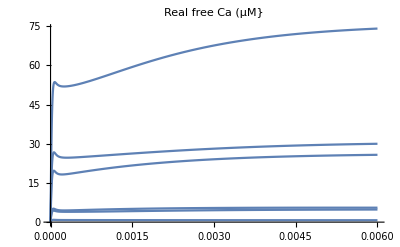

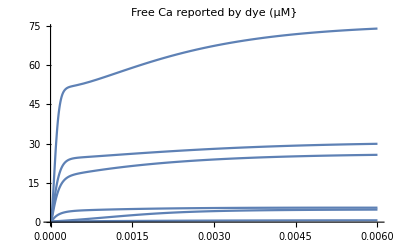

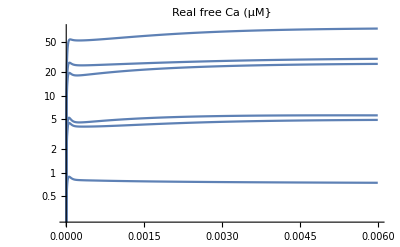

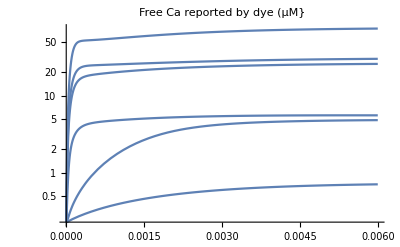

{7.03073×10^-7,4.79194×10^-6,5.53376×10^-6,0.0000257412,0.0000299583,0.0000740312}

```mathematica
Plot[10^6*CaListReal,{tt,0,TimeWindow},PlotLabel->"Real free Ca (µM}"]
Plot[10^6*CaListDye,{tt,0,TimeWindow},PlotLabel->"Free Ca reported by dye (µM}"]
LogPlot[10^6*CaListReal,{tt,0,TimeWindow},PlotLabel->"Real free Ca (µM}"]
LogPlot[10^6*CaListDye,{tt,0,TimeWindow},PlotLabel->"Free Ca reported by dye (µM}"]
CaListDyePeak=Table[NMaximize[{CaListDye[[nn]][[1]][[1]],0≤tt≤TimeWindow},tt][[1]],{nn,Length[CaListDye]}](*"[[1]][[1]]" is neede to get rid of these brackets {{}}*)
```

```mathematica
runs=Length[CaListDyePeak];
```

# Release scheme and parameters

## Define release scheme

```mathematica
nStates=4;
mat=Table[0,{nStates},{nStates}];
```

### forward rates

```mathematica
from=1;(*0 ca bound to 1 ca bound*)
kk=2kon;
mat[[from+1,from]]+=kk;mat[[from,from]]+=-kk;

from=2;(*1 ca bound to 2 ca bound*)
kk=1 kon;
mat[[from+1,from]]+=kk;mat[[from,from]]+=-kk;

from=3;(*from 2 ca bound to fused*)
kk=gamma;
mat[[from+1,from]]+=kk;mat[[from,from]]+=-kk;
```

### backwards rates

```mathematica
from=2;(*1 ca bound to 0 ca bound*)
kk=koff b^0;
mat[[from-1,from]]+=kk;mat[[from,from]]+=-kk;

from=3;(*2 ca bound to 1 ca bound*)
kk=2 koff b^1;
mat[[from-1,from]]+=kk;mat[[from,from]]+=-kk;
```

### outflux from matrix

```mathematica
mat[[1,1]]+=-kunprim;
```

### influx in matrix

```mathematica
mat[[1,1]]+=kprim/ss1[t];
```

### Matrix

```mathematica
mat//TableForm
```

-2 kon-kunprim+kprim/ss1[t] | koff | 0 | 0
2 kon | -koff-kon | 2 b koff | 0
0 | kon | -gamma-2 b koff | 0
0 | 0 | gamma | 0

## Parameters of release scheme

```mathematica
q10=2.3;
tempFact=q10^((37-24)/10);
```

```mathematica
Clear[caFunc,kprimScheme];(*Clear is needed if the cell is exectued for a 2nd time when caFunc is already set to a value or an Interpolationfunction*)

caRest=CaRest;(*227nM see above*)

affinityFactor=1.0;
konScheme=100.*caFunc[t] Sqrt[affinityFactor] tempFact 1.*^7;(*M^-1 s^-1*)
koffScheme=100.*(1/Sqrt[affinityFactor])tempFact 1500;(*s^-1*)
gammaScheme=10.*tempFact 6000;(*s^-1*)
bScheme=0.25;


KdPrim=2.*^-6;
kprimScheme = 0.6+ 30.(caFunc[t]/(KdPrim+caFunc[t]));
kunprimScheme=0.6+30.(caRest/(KdPrim+caRest));


repl={
kon -> konScheme,
koff -> koffScheme ,
gamma -> gammaScheme ,
 b-> bScheme,

kprim-> kprimScheme ,
kunprim-> kunprimScheme 

};
```

```mathematica
tauOfDecayOfUncagedCa=0.4;
```

## Initial occupancy

0.841205

0.28523

2.94922

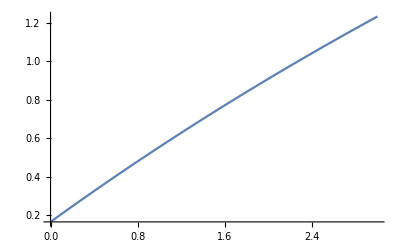

```mathematica
(*test initial equilibrium occupancy*)
caFunc[t_]:=caTmp;
fillStateSSInitial=kprimScheme/kunprimScheme;
ss0Initial=fillStateSSInitial;
(ss0Initial/.caTmp->180*^-9)
(ss0Initial/.caTmp->30*^-9)
(ss0Initial/.caTmp->180*^-9)/(ss0Initial/.caTmp->30*^-9)
(*test initial *)
Plot[kprimScheme/kunprimScheme,{caTmp,0,300*^-9}]
```

```mathematica
(*calualte initial equilibrium occupancy*)
caFunc[t_]:=caRest;
kprimScheme
kunprimScheme
ss0Initial=kprimScheme/kunprimScheme
```

3.65793

3.65793

1.

## Diff eq.

```mathematica
Clear[caFunc,eq];(*Clear is needed if the cell is exectued for a 2nd time when caFunc is already set to a value or an Interpolationfunction*)
ss[t_]={ss1[t],ss2[t],ss3[t],ss4[t]};
eq={ss'[t]==(mat/.repl).ss[t],
ss[0]=={ss0Initial,0,0,0}};
```

## Solve all states

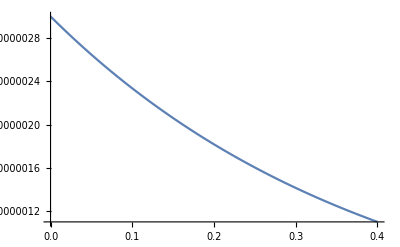

```mathematica
caFunc[t_]:=3*^-6*Exp[-t/tauOfDecayOfUncagedCa];;
Plot[caFunc[t],{t,0,0.4},PlotRange->All]
```

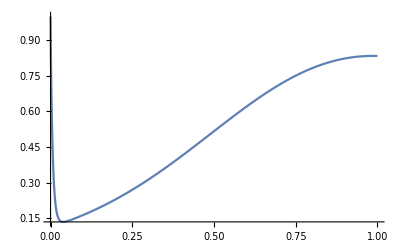

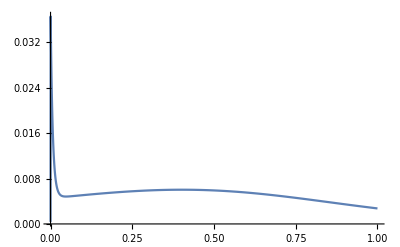

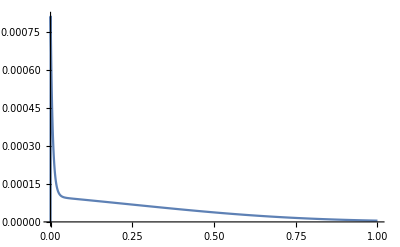

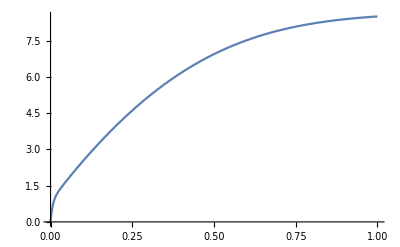

```mathematica
myNDSolveResults=NDSolve[eq,{ss1,ss2,ss3,ss4},{t,0,10.}];
tEndForPlot=1.;
Plot[(ss1[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss2[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss3[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
Plot[(ss4[t]/.myNDSolveResults),{t,0,tEndForPlot},PlotRange->All]
```

# Loop

## make lists for later

```mathematica
simCaList=Table[0,{runs}];
simParamNv=Table[0,{7},{runs}];
```

### C5

```mathematica
baselineC5=Table[{ttt,0},{ttt,cursorStart,-1*^-6,dtOfDataC5}];
(*Lists for saving data within loop*)
simParamNoiseC5=Table[0,{numberOfFitParamToBeSaved},{noiseRepeats}];
simParamMedianC5=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile1C5=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile2C5=Table[0,{numberOfFitParamToBeSaved},{runs}];
```

### C10

```mathematica
baselineC10=Table[{ttt,0},{ttt,cursorStart,-1*^-6,dtOfDataC10}];
(*Lists for saving data within loop*)
simParamNoiseC10=Table[0,{numberOfFitParamToBeSaved},{noiseRepeats}];
simParamMedianC10=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile1C10=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile2C10=Table[0,{numberOfFitParamToBeSaved},{runs}];
```

### D

```mathematica
baselineD=Table[{ttt,0},{ttt,cursorStart,-1*^-6,dtOfDataD}];
(*Lists for saving data within loop*)
simParamNoiseD=Table[0,{numberOfFitParamToBeSaved},{noiseRepeats}];
simParamMedianD=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile1D=Table[0,{numberOfFitParamToBeSaved},{runs}];
simParamQuantile2D=Table[0,{numberOfFitParamToBeSaved},{runs}];
```

### Long

```mathematica
baselineLong=Table[{ttt,0},{ttt,-0.05,-1*^-6,dtOfDataLong}];
```

## Loop

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 0.703073 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

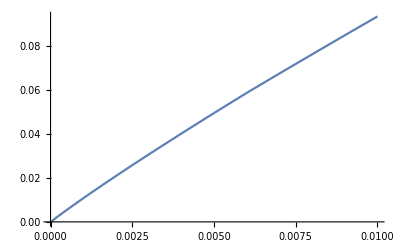

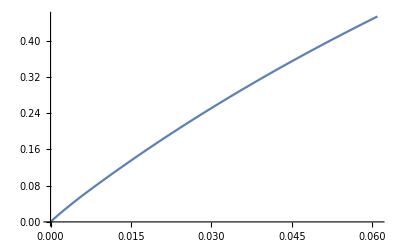

-------------------------------------------------------------------------- C5

-------------------------------------------------------------------------- C10

-------------------------------------------------------------------------- D

take mono

take mono

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

take mono

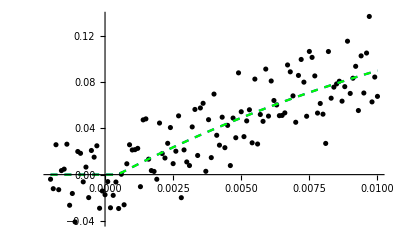

Mono: chi2 = 0.052073     d = 0.052073     a = 0.207514     t = 0.0167936

Bi: ratio chi2Mono/chi2Bi = 1.     d = 0.000470026     a = 0.21825     a1 = 0.207217     t1 =0.0167806     t2 = 1.443

Quantile::empt: Argument {} should be a non-empty list.

General::stop: Further output of Quantile::empt will be suppressed during this calculation.

Long trace was used for fitting.

take mono

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

take mono

take mono

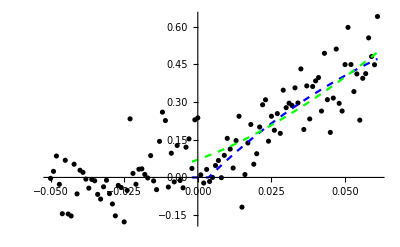

Mono: chi2 = 1.03411     d = 0.00366323     a = 0.933623     t = 0.0814763

Bi: ratio chi2Mono/chi2Bi = 1.05217     d = -0.028     a = 9.46705     a1 = -4.83606     t1 =0.147526     t2 = 0.427475

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 4.79194 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

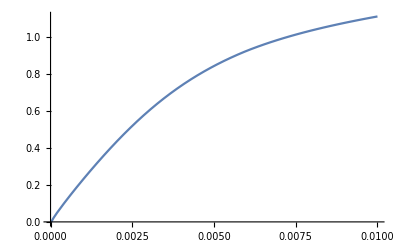

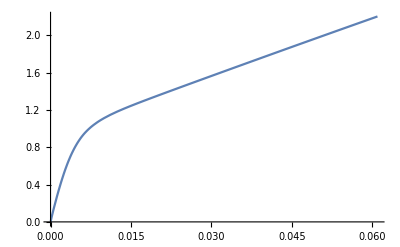

-------------------------------------------------------------------------- C5

take mono

take mono

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

take mono

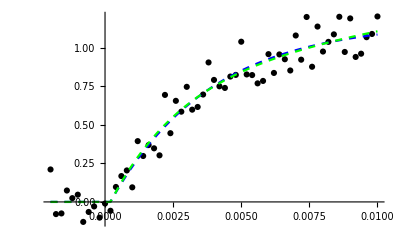

Mono: chi2 = 0.558169     d = 0.558169     a = 1.16632     t = 0.00367285

Bi: ratio chi2Mono/chi2Bi = 1.00805     d = 0.00020429     a = 7.96209     a1 = 0.840996     t1 =0.00268227     t2 = 0.238056

-------------------------------------------------------------------------- C10

take mono

take mono

take mono

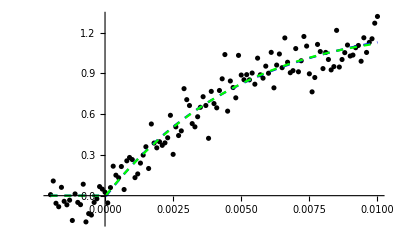

Mono: chi2 = 1.20884     d = 1.20884     a = 1.30731     t = 0.0049998

Bi: ratio chi2Mono/chi2Bi = 1.00234     d = 0.0000239968     a = 0.777713     a1 = 2.85899     t1 =0.00736634     t2 = 0.0152262

-------------------------------------------------------------------------- D

take mono

take mono

take mono

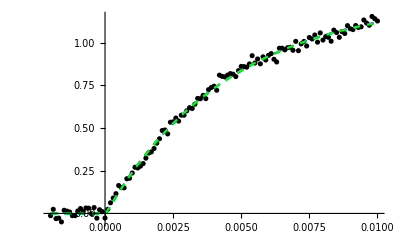

Mono: chi2 = 0.0558425     d = 0.0558425     a = 1.2585     t = 0.00453768

Bi: ratio chi2Mono/chi2Bi = 1.00026     d = 0.0000301442     a = 1.06289     a1 = 1.3005     t1 =0.00465986     t2 = 0.0742347

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 5.53376 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

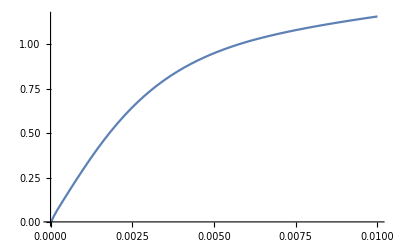

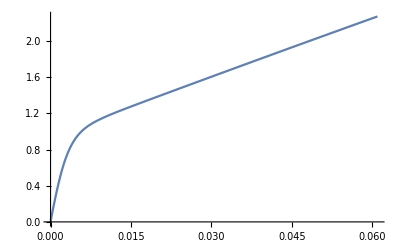

-------------------------------------------------------------------------- C5

take mono

take mono

take mono

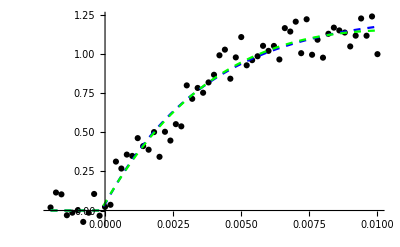

Mono: chi2 = 0.442238     d = 0.442238     a = 1.26134     t = 0.00375974

Bi: ratio chi2Mono/chi2Bi = 1.04856     d = -0.00015499     a = 0.436132     a1 = 3.67211     t1 =0.00659847     t2 = 0.0132433

-------------------------------------------------------------------------- C10

take mono

take mono

take mono

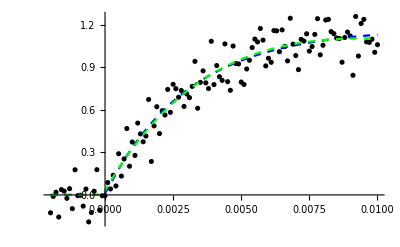

Mono: chi2 = 1.28054     d = 1.28054     a = 1.1716     t = 0.00304015

Bi: ratio chi2Mono/chi2Bi = 1.01083     d = -0.0000854457     a = 0.405774     a1 = 2.90733     t1 =0.00543144     t2 = 0.0129581

-------------------------------------------------------------------------- D

take mono

take mono

take mono

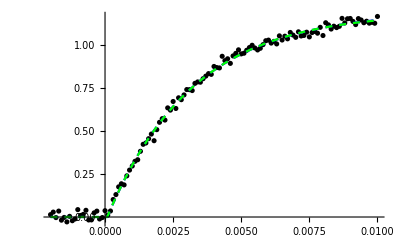

Mono: chi2 = 0.0445167     d = 0.0445167     a = 1.19823     t = 0.00312855

Bi: ratio chi2Mono/chi2Bi = 1.00155     d = 0.0000802138     a = 0.694394     a1 = 1.23061     t1 =0.00321519     t2 = 0.181744

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 25.7412 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

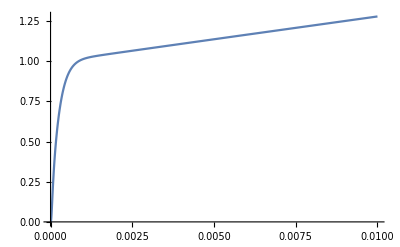

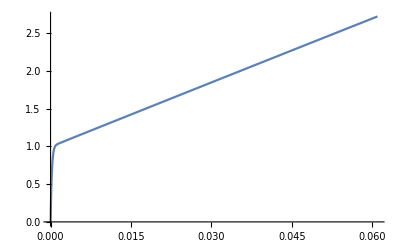

-------------------------------------------------------------------------- C5

take bi

General::munfl: Exp[-747.003] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-814.867] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-882.732] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

take bi

take bi

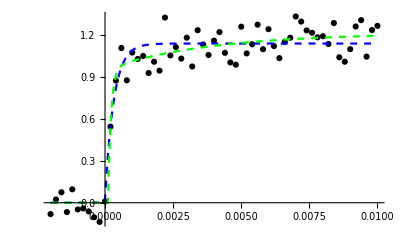

Mono: chi2 = 0.649345     d = 0.649345     a = 1.14232     t = 0.000320833

Bi: ratio chi2Mono/chi2Bi = 1.22491     d = 0.000108196     a = 1.21659     a1 = 0.964012     t1 =0.000112704     t2 = 0.00380826

-------------------------------------------------------------------------- C10

take bi

take bi

take bi

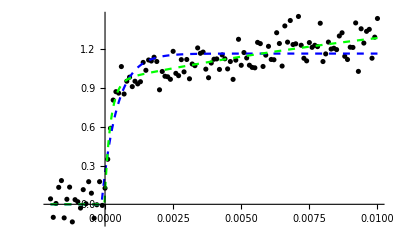

Mono: chi2 = 1.58283     d = 1.58283     a = 1.16647     t = 0.000557984

Bi: ratio chi2Mono/chi2Bi = 1.57304     d = -0.0000213642     a = 1.71711     a1 = 0.947993     t1 =0.000214065     t2 = 0.017239

-------------------------------------------------------------------------- D

take bi

take bi

take bi

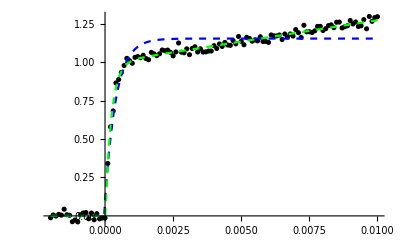

Mono: chi2 = 0.507636     d = 0.507636     a = 1.15462     t = 0.000401872

Bi: ratio chi2Mono/chi2Bi = 10.5369     d = 9.09647×10^-6     a = 10.4532     a1 = 0.994364     t1 =0.000224212     t2 = 0.332725

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 29.9583 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

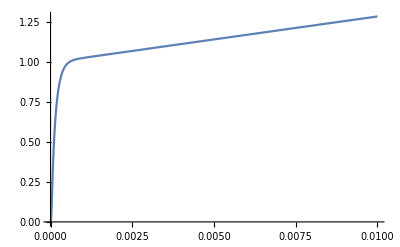

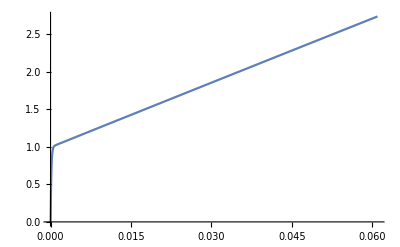

-------------------------------------------------------------------------- C5

take bi

take bi

take bi

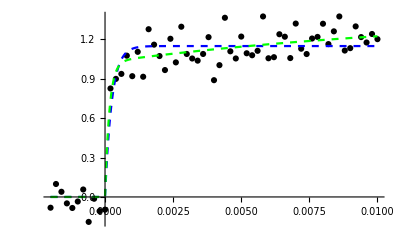

Mono: chi2 = 0.786886     d = 0.786886     a = 1.14792     t = 0.000248599

Bi: ratio chi2Mono/chi2Bi = 1.24222     d = -1.03232×10^-15     a = 1.38662     a1 = 1.02517     t1 =0.000160952     t2 = 0.0126743

-------------------------------------------------------------------------- C10

take bi

take bi

take bi

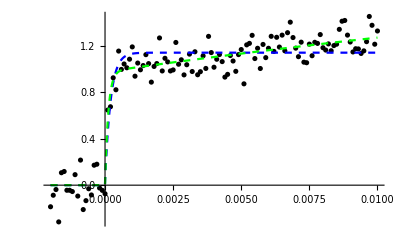

Mono: chi2 = 1.91997     d = 1.91997     a = 1.13967     t = 0.00020587

Bi: ratio chi2Mono/chi2Bi = 1.4426     d = -7.85951×10^-18     a = 2.24612     a1 = 0.97525     t1 =0.000120365     t2 = 0.0380236

-------------------------------------------------------------------------- D

take bi

take bi

take bi

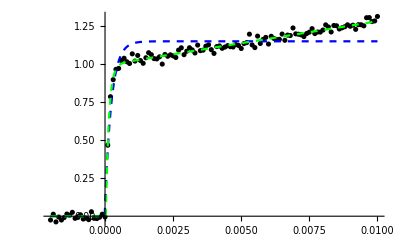

Mono: chi2 = 0.614661     d = 0.614661     a = 1.14859     t = 0.000235357

Bi: ratio chi2Mono/chi2Bi = 13.2444     d = 0.0000270937     a = 11.6767     a1 = 0.991481     t1 =0.000114976     t2 = 0.364136

-------------------------------------------------------------------------------------------------------------

----------------    Ca = 74.0312 uM         --------------------------------------------------------

-------------------------------------------------------------------------------------------------------------

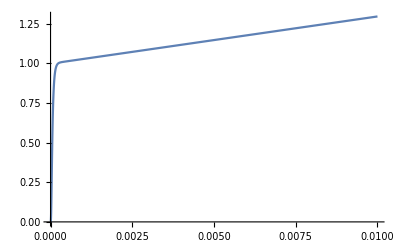

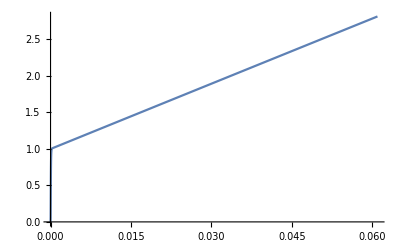

-------------------------------------------------------------------------- C5

take bi

take bi

take mono

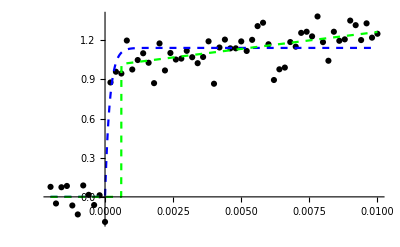

Mono: chi2 = 0.857236     d = 0.857236     a = 1.14183     t = 0.000173996

Bi: ratio chi2Mono/chi2Bi = 0.37743     d = 0.000595672     a = 10.783     a1 = 1.01854     t1 =1.64419×10^-6     t2 = 0.369272

-------------------------------------------------------------------------- C10

take bi

take bi

take bi

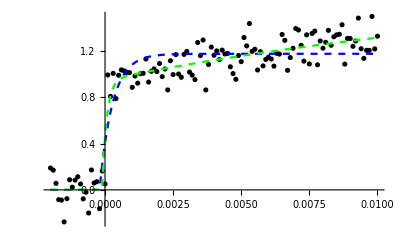

Mono: chi2 = 2.45429     d = 2.45429     a = 1.17529     t = 0.000473998

Bi: ratio chi2Mono/chi2Bi = 1.49977     d = -0.000108107     a = 1.83289     a1 = 0.94555     t1 =0.000168777     t2 = 0.0188063

-------------------------------------------------------------------------- D

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

take bi

take bi

take bi

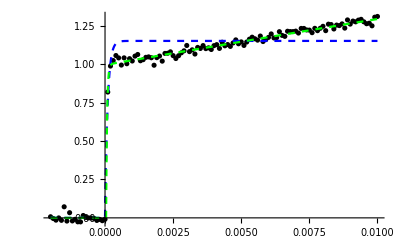

Mono: chi2 = 0.729864     d = 0.729864     a = 1.15262     t = 0.000096565

Bi: ratio chi2Mono/chi2Bi = 17.9428     d = 0.0000391999     a = 8.27077     a1 = 0.997597     t1 =0.0000355141     t2 = 0.238329

```mathematica
For[r=1,r≤runs,r+=1,
myCaNow=CaListDyePeak[[r]];
lastSimulatedCaListReal=CaListReal[[r]][[1]][[1]]/.tt->TimeWindow;(*"[[1]][[1]]" is neede to get rid of these brackets {{}}*)
Print["-------------------------------------------------------------------------------------------------------------"];Print["----------------    Ca = ",1*^6 myCaNow," uM         --------------------------------------------------------"];Print["-------------------------------------------------------------------------------------------------------------"];
simCaList[[r]]=myCaNow;
caFunc[ttt_]:=If[ttt<TimeWindow,
CaListReal[[r]][[1]][[1]]/.tt->ttt,(*tt because this is the symbol used in "Calculate Ca transients"*)
lastSimulatedCaListReal*Exp[-ttt/tauOfDecayOfUncagedCa]
];
(* solve Diff Eq.: *)
myNDSolveResults=NDSolve[eq,ss4,{t,0,0.4}]; 
(* plot results: *)
fused[t_]:=ss4[t];
Plot[(fused[t]/.myNDSolveResults),{t,0,cursorEnd},PlotRange->All]//Print;
Plot[(fused[t]/.myNDSolveResults),{t,0,cursorEndLong},PlotRange->All]//Print;
If[exportYes==1,
toExport=Table[{t,(fused[t]/.myNDSolveResults)[[1]]},{t,0.,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" withoutNoise.txt",toExport,"Table"];
];
(* sample data and add baseline: --------*)
tmpCumRelC5=Table[{ttt,(fused[ttt]/.myNDSolveResults)[[1]]},{ttt,0.,cursorEnd,dtOfDataC5}];
tmpToFitC5=Catenate[{baselineC5,tmpCumRelC5}];
tmpCumRelC10=Table[{ttt,(fused[ttt]/.myNDSolveResults)[[1]]},{ttt,0.,cursorEnd,dtOfDataC10}];
tmpToFitC10=Catenate[{baselineC10,tmpCumRelC10}];
tmpCumRelD=Table[{ttt,(fused[ttt]/.myNDSolveResults)[[1]]},{ttt,0.,cursorEnd,dtOfDataD}];
tmpToFitD=Catenate[{baselineD,tmpCumRelD}];
tmpCumRelLong=Table[{ttt,(fused[ttt]/.myNDSolveResults)[[1]]},{ttt,0.,cursorEndLong,dtOfDataLong}];
tmpToFitLong=Catenate[{baselineLong,tmpCumRelLong}];

(*---------    get amplitude without noise and without fitting -----------------*)
For[NvCount=1,NvCount≤7,NvCount+=1,
simParamNv[[NvCount,r]]=(fused[timeOfNv[[NvCount]]]/.myNDSolveResults)[[1]];(* the [[1]] is somehow needed to get rid of a list structure probably related to the interpolate function*)
];

(*--------------   Startvalues for fit the same for all C5 C10 and D -------------*)
caAdjustedTau1Guess=tau1Guess/((myCaNow/10.*^-6)^4);
caAdjustedTau1Guess=tau1Guess/((myCaNow/10.*^-6)^1);
caAdjustedTau2Guess=10 caAdjustedTau1Guess;
caAdjustedDelayGuess=delayGuess/((myCaNow/10.*^-6)^1);

(*---------    Fitting of data, saving of results, and plotting-----------------*)
(*-----------------------------------------------------------------------------*)
(*--------------------------------------    C5     ----------------------------*)
(*-----------------------------------------------------------------------------*)
Print["-------------------------------------------------------------------------- C5"];
(*check that signal is large enough relative to noise to obtain useful fit results. If not, do not do fitting and set everything to {}*)
If[simParamNv[[5,r]] > signalToNoiseRatioC5 myNoiseC5,(*add noise and do the fitting several times and then average the results*)
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
(*Print[noiseN];*)
tmpToFitNoise=Transpose[{tmpToFitC5[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseC5]]&/@tmpToFitC5[[All,2]]}];
(*fit mono-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoise, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultMono=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC5[[1,noiseN]]=0;(*not used anymore*)
simParamNoiseC5[[2,noiseN]]=fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
(*Print[fitResultsTMP["ANOVATableSumsOfSquares"]];*)
simParamNoiseC5[[3,noiseN]]=(delayMono/.fitResultMono)[[1]];
simParamNoiseC5[[4,noiseN]]=((ampMono/.fitResultMono))[[1]];
simParamNoiseC5[[5,noiseN]]=(1/(tau1Mono/.fitResultMono))[[1]];
(*fit bi-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoise, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultBi=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC5[[6,noiseN]]=simParamNoiseC5[[2,noiseN]]/fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
simParamNoiseC5[[7,noiseN]]=(delay/.fitResultBi)[[1]];
simParamNoiseC5[[8,noiseN]]=((amp/.fitResultBi))[[1]];
simParamNoiseC5[[9,noiseN]]=((amp amp1/.fitResultBi))[[1]];(*relative amp1*)
simParamNoiseC5[[10,noiseN]]=(1/(tau1/.fitResultBi))[[1]];
simParamNoiseC5[[11,noiseN]]=(1/(tau2/.fitResultBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseC5[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseC5[[11,noiseN]]/simParamNoiseC5[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseC5[[12,noiseN]]=simParamNoiseC5[[7,noiseN]];(*delay*)
simParamNoiseC5[[13,noiseN]]=simParamNoiseC5[[8,noiseN]];(*amp*)
simParamNoiseC5[[14,noiseN]]=simParamNoiseC5[[9,noiseN]];(*amp1*)
simParamNoiseC5[[15,noiseN]]=simParamNoiseC5[[10,noiseN]];(*tau1*)
simParamNoiseC5[[16,noiseN]]=simParamNoiseC5[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseC5[[12,noiseN]]=simParamNoiseC5[[3,noiseN]];(*delay*)
simParamNoiseC5[[13,noiseN]]=simParamNoiseC5[[4,noiseN]];(*amp*)
simParamNoiseC5[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseC5[[15,noiseN]]=simParamNoiseC5[[5,noiseN]];(*tau1*)
simParamNoiseC5[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoise,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultMono,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultBi,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 data.txt",tmpToFitNoise,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultMono)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 fitMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultBi)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 fitBi.txt",toExport,"Table"];
];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseC5[[2,noiseN]],"     d = ",simParamNoiseC5[[2,noiseN]],"     a = ",simParamNoiseC5[[4,noiseN]],"     t = ",1/simParamNoiseC5[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseC5[[6,noiseN]],"     d = ",simParamNoiseC5[[7,noiseN]],"     a = ",simParamNoiseC5[[8,noiseN]],"     a1 = ",simParamNoiseC5[[9,noiseN]],"     t1 =",1/simParamNoiseC5[[10,noiseN]],"     t2 = ",1/simParamNoiseC5[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC5[[p,r]]=Median[simParamNoiseC5[[p,All]]/.NaN->Sequence[]];
simParamQuantile1C5[[p,r]]=Quantile[simParamNoiseC5[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2C5[[p,r]]=Quantile[simParamNoiseC5[[p,All]]/.NaN->Sequence[],myQuantile2];
];

(*if tau1 merge > 10 ms, use long trace for fitting*)
If[(1/simParamMedianC5[[15,r]])>0.01,
Print["Long trace was used for fitting."];
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
tmpToFitNoiseLong=Transpose[{tmpToFitLong[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseLong]]&/@tmpToFitLong[[All,2]]}];
(*fit mono-exp to Long trace*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoiseLong, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongMono=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC5[[2,noiseN]]=fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
(*Print[fitResultsTMP["ANOVATableSumsOfSquares"]];*)
simParamNoiseC5[[3,noiseN]]=(delayMono/.fitResultLongMono)[[1]];
simParamNoiseC5[[4,noiseN]]=((ampMono/.fitResultLongMono))[[1]];
simParamNoiseC5[[5,noiseN]]=(1/(tau1Mono/.fitResultLongMono))[[1]];
(*fit bi-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoiseLong, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongBi=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC5[[6,noiseN]]=simParamNoiseC5[[2,noiseN]]/fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
simParamNoiseC5[[7,noiseN]]=(delay/.fitResultLongBi)[[1]];
simParamNoiseC5[[8,noiseN]]=((amp/.fitResultLongBi))[[1]];
simParamNoiseC5[[9,noiseN]]=((amp amp1/.fitResultLongBi))[[1]];(*relative amp1*)
simParamNoiseC5[[10,noiseN]]=(1/(tau1/.fitResultLongBi))[[1]];
simParamNoiseC5[[11,noiseN]]=(1/(tau2/.fitResultLongBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseC5[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseC5[[11,noiseN]]/simParamNoiseC5[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultLongBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultLongBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseC5[[12,noiseN]]=simParamNoiseC5[[7,noiseN]];(*delay*)
simParamNoiseC5[[13,noiseN]]=simParamNoiseC5[[8,noiseN]];(*amp*)
simParamNoiseC5[[14,noiseN]]=simParamNoiseC5[[9,noiseN]];(*amp1*)
simParamNoiseC5[[15,noiseN]]=simParamNoiseC5[[10,noiseN]];(*tau1*)
simParamNoiseC5[[16,noiseN]]=simParamNoiseC5[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseC5[[12,noiseN]]=simParamNoiseC5[[3,noiseN]];(*delay*)
simParamNoiseC5[[13,noiseN]]=simParamNoiseC5[[4,noiseN]];(*amp*)
simParamNoiseC5[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseC5[[15,noiseN]]=simParamNoiseC5[[5,noiseN]];(*tau1*)
simParamNoiseC5[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoiseLong,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultLongMono,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultLongBi,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 dataLong.txt",tmpToFitNoiseLong,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultLongMono)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 fitLongMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultLongBi)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C5 fitLongBi.txt",toExport,"Table"];

];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseC5[[2,noiseN]],"     d = ",simParamNoiseC5[[3,noiseN]],"     a = ",simParamNoiseC5[[4,noiseN]],"     t = ",1/simParamNoiseC5[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseC5[[6,noiseN]],"     d = ",simParamNoiseC5[[7,noiseN]],"     a = ",simParamNoiseC5[[8,noiseN]],"     a1 = ",simParamNoiseC5[[9,noiseN]],"     t1 =",1/simParamNoiseC5[[10,noiseN]],"     t2 = ",1/simParamNoiseC5[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC5[[p,r]]=Median[simParamNoiseC5[[p,All]]/.NaN->Sequence[]];
simParamQuantile1C5[[p,r]]=Quantile[simParamNoiseC5[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2C5[[p,r]]=Quantile[simParamNoiseC5[[p,All]]/.NaN->Sequence[],myQuantile2];
];
];

,(*else: signal is not large enough*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC5[[p,r]]={};
simParamQuantile1C5[[p,r]]={};
simParamQuantile2C5[[p,r]]={};
];
];


(*---------    Fitting of data, saving of results, and plotting-----------------*)
(*-----------------------------------------------------------------------------*)
(*--------------------------------------    C10     ----------------------------*)
(*-----------------------------------------------------------------------------*)
Print["-------------------------------------------------------------------------- C10"];
(*check that signal is large enough relative to noise to obtain useful fit results. If not, do not do fitting and set everything to {}*)
If[simParamNv[[5,r]] > signalToNoiseRatioC10 myNoiseC10,(*add noise several times and do the fitting and than average the results*)
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
(*Print[noiseN];*)
tmpToFitNoise=Transpose[{tmpToFitC10[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseC10]]&/@tmpToFitC10[[All,2]]}];
(*fit mono-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoise, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultMono=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC10[[1,noiseN]]=0;(*not used anymore*)
simParamNoiseC10[[2,noiseN]]=fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
(*Print[fitResultsTMP["ANOVATableSumsOfSquares"]];*)
simParamNoiseC10[[3,noiseN]]=(delayMono/.fitResultMono)[[1]];
simParamNoiseC10[[4,noiseN]]=((ampMono/.fitResultMono))[[1]];
simParamNoiseC10[[5,noiseN]]=(1/(tau1Mono/.fitResultMono))[[1]];
(*fit bi-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoise, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultBi=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC10[[6,noiseN]]=simParamNoiseC10[[2,noiseN]]/fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
simParamNoiseC10[[7,noiseN]]=(delay/.fitResultBi)[[1]];
simParamNoiseC10[[8,noiseN]]=((amp/.fitResultBi))[[1]];
simParamNoiseC10[[9,noiseN]]=((amp amp1/.fitResultBi))[[1]];(*relative amp1*)
simParamNoiseC10[[10,noiseN]]=(1/(tau1/.fitResultBi))[[1]];
simParamNoiseC10[[11,noiseN]]=(1/(tau2/.fitResultBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseC10[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseC10[[11,noiseN]]/simParamNoiseC10[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseC10[[12,noiseN]]=simParamNoiseC10[[7,noiseN]];(*delay*)
simParamNoiseC10[[13,noiseN]]=simParamNoiseC10[[8,noiseN]];(*amp*)
simParamNoiseC10[[14,noiseN]]=simParamNoiseC10[[9,noiseN]];(*amp1*)
simParamNoiseC10[[15,noiseN]]=simParamNoiseC10[[10,noiseN]];(*tau1*)
simParamNoiseC10[[16,noiseN]]=simParamNoiseC10[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseC10[[12,noiseN]]=simParamNoiseC10[[3,noiseN]];(*delay*)
simParamNoiseC10[[13,noiseN]]=simParamNoiseC10[[4,noiseN]];(*amp*)
simParamNoiseC10[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseC10[[15,noiseN]]=simParamNoiseC10[[5,noiseN]];(*tau1*)
simParamNoiseC10[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoise,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultMono,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultBi,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 data.txt",tmpToFitNoise,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultMono)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 fitMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultBi)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 fitBi.txt",toExport,"Table"];
];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseC10[[2,noiseN]],"     d = ",simParamNoiseC10[[2,noiseN]],"     a = ",simParamNoiseC10[[4,noiseN]],"     t = ",1/simParamNoiseC10[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseC10[[6,noiseN]],"     d = ",simParamNoiseC10[[7,noiseN]],"     a = ",simParamNoiseC10[[8,noiseN]],"     a1 = ",simParamNoiseC10[[9,noiseN]],"     t1 =",1/simParamNoiseC10[[10,noiseN]],"     t2 = ",1/simParamNoiseC10[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC10[[p,r]]=Median[simParamNoiseC10[[p,All]]/.NaN->Sequence[]];
simParamQuantile1C10[[p,r]]=Quantile[simParamNoiseC10[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2C10[[p,r]]=Quantile[simParamNoiseC10[[p,All]]/.NaN->Sequence[],myQuantile2];
];

(*if tau1 merge > 10 ms, use long trace for fitting*)
If[(1/simParamMedianC10[[15,r]])>0.01,
Print["Long trace was used for fitting."];
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
tmpToFitNoiseLong=Transpose[{tmpToFitLong[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseLong]]&/@tmpToFitLong[[All,2]]}];
(*fit mono-exp to Long trace*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoiseLong, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongMono=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC10[[2,noiseN]]=fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
(*Print[fitResultsTMP["ANOVATableSumsOfSquares"]];*)
simParamNoiseC10[[3,noiseN]]=(delayMono/.fitResultLongMono)[[1]];
simParamNoiseC10[[4,noiseN]]=((ampMono/.fitResultLongMono))[[1]];
simParamNoiseC10[[5,noiseN]]=(1/(tau1Mono/.fitResultLongMono))[[1]];
(*fit bi-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoiseLong, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongBi=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseC10[[6,noiseN]]=simParamNoiseC10[[2,noiseN]]/fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
simParamNoiseC10[[7,noiseN]]=(delay/.fitResultLongBi)[[1]];
simParamNoiseC10[[8,noiseN]]=((amp/.fitResultLongBi))[[1]];
simParamNoiseC10[[9,noiseN]]=((amp amp1/.fitResultLongBi))[[1]];(*relative amp1*)
simParamNoiseC10[[10,noiseN]]=(1/(tau1/.fitResultLongBi))[[1]];
simParamNoiseC10[[11,noiseN]]=(1/(tau2/.fitResultLongBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseC10[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseC10[[11,noiseN]]/simParamNoiseC10[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultLongBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultLongBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseC10[[12,noiseN]]=simParamNoiseC10[[7,noiseN]];(*delay*)
simParamNoiseC10[[13,noiseN]]=simParamNoiseC10[[8,noiseN]];(*amp*)
simParamNoiseC10[[14,noiseN]]=simParamNoiseC10[[9,noiseN]];(*amp1*)
simParamNoiseC10[[15,noiseN]]=simParamNoiseC10[[10,noiseN]];(*tau1*)
simParamNoiseC10[[16,noiseN]]=simParamNoiseC10[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseC10[[12,noiseN]]=simParamNoiseC10[[3,noiseN]];(*delay*)
simParamNoiseC10[[13,noiseN]]=simParamNoiseC10[[4,noiseN]];(*amp*)
simParamNoiseC10[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseC10[[15,noiseN]]=simParamNoiseC10[[5,noiseN]];(*tau1*)
simParamNoiseC10[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoiseLong,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultLongMono,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultLongBi,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 dataLong.txt",tmpToFitNoiseLong,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultLongMono)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 fitLongMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultLongBi)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" C10 fitLongBi.txt",toExport,"Table"];

];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseC10[[2,noiseN]],"     d = ",simParamNoiseC10[[3,noiseN]],"     a = ",simParamNoiseC10[[4,noiseN]],"     t = ",1/simParamNoiseC10[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseC10[[6,noiseN]],"     d = ",simParamNoiseC10[[7,noiseN]],"     a = ",simParamNoiseC10[[8,noiseN]],"     a1 = ",simParamNoiseC10[[9,noiseN]],"     t1 =",1/simParamNoiseC10[[10,noiseN]],"     t2 = ",1/simParamNoiseC10[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC10[[p,r]]=Median[simParamNoiseC10[[p,All]]/.NaN->Sequence[]];
simParamQuantile1C10[[p,r]]=Quantile[simParamNoiseC10[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2C10[[p,r]]=Quantile[simParamNoiseC10[[p,All]]/.NaN->Sequence[],myQuantile2];
];
];

,(*else: signal is not large enough*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianC10[[p,r]]={};
simParamQuantile1C10[[p,r]]={};
simParamQuantile2C10[[p,r]]={};
];
];

(*---------    Fitting of data, saving of results, and plotting-----------------*)
(*-----------------------------------------------------------------------------*)
(*--------------------------------------    D     ----------------------------*)
(*-----------------------------------------------------------------------------*)
Print["-------------------------------------------------------------------------- D"];
(*check that signal is large enough relative to noise to obtain useful fit results. If not, do not do fitting and set everything to {}*)
If[simParamNv[[5,r]] > signalToNoiseRatioD myNoiseD,(*add noise several times and do the fitting and than average the results*)
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
(*Print[noiseN];*)
tmpToFitNoise=Transpose[{tmpToFitD[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseD]]&/@tmpToFitD[[All,2]]}];
(*fit mono-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoise, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultMono=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseD[[1,noiseN]]=0;(*not used anymore*)
simParamNoiseD[[2,noiseN]]=fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
(*Print[fitResultsTMP["ANOVATableSumsOfSquares"]];*)
simParamNoiseD[[3,noiseN]]=(delayMono/.fitResultMono)[[1]];
simParamNoiseD[[4,noiseN]]=((ampMono/.fitResultMono))[[1]];
simParamNoiseD[[5,noiseN]]=(1/(tau1Mono/.fitResultMono))[[1]];
(*fit bi-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoise, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultBi=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseD[[6,noiseN]]=simParamNoiseD[[2,noiseN]]/fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
simParamNoiseD[[7,noiseN]]=(delay/.fitResultBi)[[1]];
simParamNoiseD[[8,noiseN]]=((amp/.fitResultBi))[[1]];
simParamNoiseD[[9,noiseN]]=((amp amp1/.fitResultBi))[[1]];(*relative amp1*)
simParamNoiseD[[10,noiseN]]=(1/(tau1/.fitResultBi))[[1]];
simParamNoiseD[[11,noiseN]]=(1/(tau2/.fitResultBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseD[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseD[[11,noiseN]]/simParamNoiseD[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseD[[12,noiseN]]=simParamNoiseD[[7,noiseN]];(*delay*)
simParamNoiseD[[13,noiseN]]=simParamNoiseD[[8,noiseN]];(*amp*)
simParamNoiseD[[14,noiseN]]=simParamNoiseD[[9,noiseN]];(*amp1*)
simParamNoiseD[[15,noiseN]]=simParamNoiseD[[10,noiseN]];(*tau1*)
simParamNoiseD[[16,noiseN]]=simParamNoiseD[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseD[[12,noiseN]]=simParamNoiseD[[3,noiseN]];(*delay*)
simParamNoiseD[[13,noiseN]]=simParamNoiseD[[4,noiseN]];(*amp*)
simParamNoiseD[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseD[[15,noiseN]]=simParamNoiseD[[5,noiseN]];(*tau1*)
simParamNoiseD[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoise,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultMono,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultBi,{x1,cursorStart,cursorEnd},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D data.txt",tmpToFitNoise,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultMono)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D fitMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultBi)[[1]]},{t,cursorStart,cursorEnd,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D fitBi.txt",toExport,"Table"];
];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseD[[2,noiseN]],"     d = ",simParamNoiseD[[2,noiseN]],"     a = ",simParamNoiseD[[4,noiseN]],"     t = ",1/simParamNoiseD[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseD[[6,noiseN]],"     d = ",simParamNoiseD[[7,noiseN]],"     a = ",simParamNoiseD[[8,noiseN]],"     a1 = ",simParamNoiseD[[9,noiseN]],"     t1 =",1/simParamNoiseD[[10,noiseN]],"     t2 = ",1/simParamNoiseD[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianD[[p,r]]=Median[simParamNoiseD[[p,All]]/.NaN->Sequence[]];
simParamQuantile1D[[p,r]]=Quantile[simParamNoiseD[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2D[[p,r]]=Quantile[simParamNoiseD[[p,All]]/.NaN->Sequence[],myQuantile2];
];

(*if tau1 merge > 10 ms, use long trace for fitting*)
If[(1/simParamMedianD[[15,r]])>0.01,
Print["Long trace was used for fitting."];
For[noiseN=1,noiseN≤ noiseRepeats,noiseN+=1,
tmpToFitNoiseLong=Transpose[{tmpToFitLong[[All,1]],#+RandomVariate[NormalDistribution[0,myNoiseLong]]&/@tmpToFitLong[[All,2]]}];
(*fit mono-exp to Long trace*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoiseLong, myFitMono[x1],  {{delayMono, delayGuess},{ampMono, ampGuess},{tau1Mono, caAdjustedTau1Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongMono=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseD[[2,noiseN]]=fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
(*Print[fitResultsTMP["ANOVATableSumsOfSquares"]];*)
simParamNoiseD[[3,noiseN]]=(delayMono/.fitResultLongMono)[[1]];
simParamNoiseD[[4,noiseN]]=((ampMono/.fitResultLongMono))[[1]];
simParamNoiseD[[5,noiseN]]=(1/(tau1Mono/.fitResultLongMono))[[1]];
(*fit bi-exp*)
fitResultsTMP=NonlinearModelFit[tmpToFitNoiseLong, myFitBi[x1],  {{delay, delayGuess},{amp, ampGuess},{amp1, amp1Guess},{tau1, caAdjustedTau1Guess},{tau2, caAdjustedTau2Guess}},x1, MaxIterations -> myMaxIterations];
fitResultLongBi=fitResultsTMP[{"BestFitParameters"}];
simParamNoiseD[[6,noiseN]]=simParamNoiseD[[2,noiseN]]/fitResultsTMP["ANOVATableSumsOfSquares"][[2]];
simParamNoiseD[[7,noiseN]]=(delay/.fitResultLongBi)[[1]];
simParamNoiseD[[8,noiseN]]=((amp/.fitResultLongBi))[[1]];
simParamNoiseD[[9,noiseN]]=((amp amp1/.fitResultLongBi))[[1]];(*relative amp1*)
simParamNoiseD[[10,noiseN]]=(1/(tau1/.fitResultLongBi))[[1]];
simParamNoiseD[[11,noiseN]]=(1/(tau2/.fitResultLongBi))[[1]];
(*merge*)
If[
(*to use the bi-exp fit, the following cirteria should be fullfilled:*)
(*chi2 should improve(=decrease) by >4%*)
(simParamNoiseD[[6,noiseN]]>1.04)
&&
(*tau1 and tau2 of bi fit should be factor of >3 different*)
((simParamNoiseD[[11,noiseN]]/simParamNoiseD[[10,noiseN]])<3.)
&&
(*relative amplitude of 1st component should be > 5% *)
((( amp1/.fitResultLongBi))[[1]]>0.05)
&&
(*relative amplitude of 1st component should be < 95% *)
((( amp1/.fitResultLongBi))[[1]]<0.95)
,
(*take bi*)
Print["take bi"];
simParamNoiseD[[12,noiseN]]=simParamNoiseD[[7,noiseN]];(*delay*)
simParamNoiseD[[13,noiseN]]=simParamNoiseD[[8,noiseN]];(*amp*)
simParamNoiseD[[14,noiseN]]=simParamNoiseD[[9,noiseN]];(*amp1*)
simParamNoiseD[[15,noiseN]]=simParamNoiseD[[10,noiseN]];(*tau1*)
simParamNoiseD[[16,noiseN]]=simParamNoiseD[[11,noiseN]];(*tau2*)
,
(*take mono*)
Print["take mono"];
simParamNoiseD[[12,noiseN]]=simParamNoiseD[[3,noiseN]];(*delay*)
simParamNoiseD[[13,noiseN]]=simParamNoiseD[[4,noiseN]];(*amp*)
simParamNoiseD[[14,noiseN]]=NaN;(*amp1*)
simParamNoiseD[[15,noiseN]]=simParamNoiseD[[5,noiseN]];(*tau1*)
simParamNoiseD[[16,noiseN]]=NaN;(*tau2*)
];
];
(*plot last example of the noise loop*)
gr1=ListPlot[tmpToFitNoiseLong,PlotRange->All,PlotStyle->Black];
gr2=Plot[myFitMono[x1]/.fitResultLongMono,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Blue,Dashed}];
gr3=Plot[myFitBi[x1]/.fitResultLongBi,{x1,cursorStart,cursorEndLong},PlotRange->All,PlotStyle->{Green,Dashed}];
Show[gr1,gr2,gr3,PlotRange->All ]//Print;
If[exportYes==1,
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D dataLong.txt",tmpToFitNoiseLong,"Table"];
toExport=Table[{t,(myFitMono[t]/.fitResultLongMono)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D fitLongMono.txt",toExport,"Table"];
toExport=Table[{t,(myFitBi[t]/.fitResultLongBi)[[1]]},{t,cursorStart,cursorEndLong,dtOfPlotsForExport}];
Export["withinLoop r"<>ToString[r]<>" Ca"<>ToString[1*^6 myCaNow]<>" D fitLongBi.txt",toExport,"Table"];

];
noiseN=noiseRepeats;(*fit parameter of last noisetrace*)
Print["Mono: chi2 = ",simParamNoiseD[[2,noiseN]],"     d = ",simParamNoiseD[[3,noiseN]],"     a = ",simParamNoiseD[[4,noiseN]],"     t = ",1/simParamNoiseD[[5,noiseN]]];
Print["Bi: ratio chi2Mono/chi2Bi = ",simParamNoiseD[[6,noiseN]],"     d = ",simParamNoiseD[[7,noiseN]],"     a = ",simParamNoiseD[[8,noiseN]],"     a1 = ",simParamNoiseD[[9,noiseN]],"     t1 =",1/simParamNoiseD[[10,noiseN]],"     t2 = ",1/simParamNoiseD[[11,noiseN]]];
(*average fit results*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianD[[p,r]]=Median[simParamNoiseD[[p,All]]/.NaN->Sequence[]];
simParamQuantile1D[[p,r]]=Quantile[simParamNoiseD[[p,All]]/.NaN->Sequence[],myQuantile1];simParamQuantile2D[[p,r]]=Quantile[simParamNoiseD[[p,All]]/.NaN->Sequence[],myQuantile2];
];
];

,(*else: signal is not large enough*)
For[p=1,p≤numberOfFitParamToBeSaved,p+=1,
simParamMedianD[[p,r]]={};
simParamQuantile1D[[p,r]]={};
simParamQuantile2D[[p,r]]={};
];
];
];
```

# Plots

```mathematica
rrp=10;
```

```mathematica
caFact=1*^6;
```

```mathematica
colorA=Green;
colorB=Red;
colorC=Blue;
```

## release rate 1/tau1 (merge of mono 1/tau and bi 1/tau1)

```mathematica
simParam=15;
```

### C5

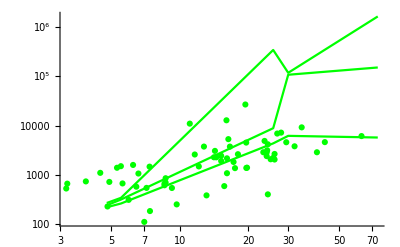

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca, dataT1C5RelRate}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau1 C5 data.txt",Transpose[{dataT1C5Ca, dataT1C5RelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]],simParamMedianC5[[simParam,All]],simParamQuantile2C5[[simParam,All]]}];
Export["plot InvTau1 C5 fit - quantiles and median.txt",toExport,"Table"];
];
```

### C10

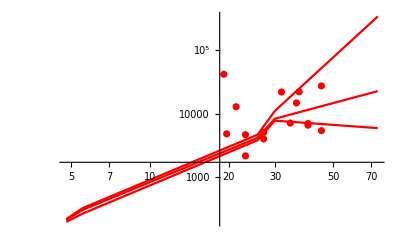

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca, dataT1C10RelRate}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau1 C10 data.txt",Transpose[{dataT1C10Ca, dataT1C10RelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]],simParamMedianC10[[simParam,All]],simParamQuantile2C10[[simParam,All]]}];
Export["plot InvTau1 C10 fit - quantiles and median.txt",toExport,"Table"];
];
```

### D

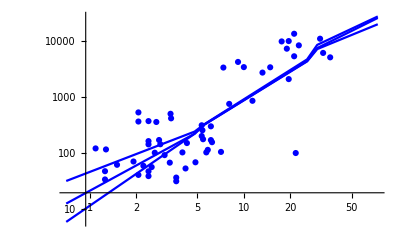

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT1DCa, dataT1DRelRate}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianD[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau1 D data.txt",Transpose[{dataT1DCa, dataT1DRelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]],simParamMedianD[[simParam,All]],simParamQuantile2D[[simParam,All]]}];
Export["plot InvTau1 D fit - quantiles and median.txt",toExport,"Table"];
];
```

### C5 and C10 and D

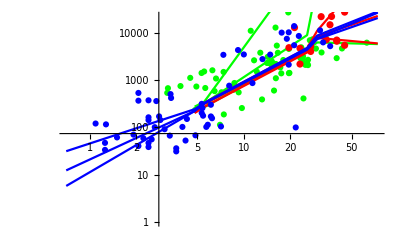

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{All,{0,10}}]
```

```mathematica
Show[gr1a,gr1b,gr1c,PlotRange->{All,{2,10}}];
```

## delay (mono and bi merged)

```mathematica
simParam=12;
```

```mathematica
Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}]//TableForm
```

0.703073 | 
4.79194 | 0.000196264
5.53376 | 9.28401×10^-6
25.7412 | 0.000108196
29.9583 | 0.00018539
74.0312 | -8.5×10^-18

### C5

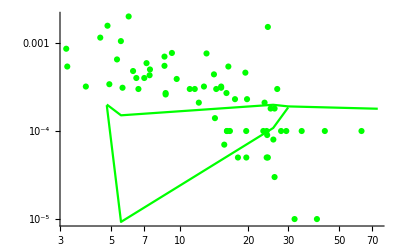

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca, dataT1C5Delay}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
If[exportYes==1,
Export["plot delay C5 data.txt",Transpose[{dataT1C5Ca, dataT1C5Delay}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]],simParamMedianC5[[simParam,All]],simParamQuantile2C5[[simParam,All]]}];
Export["plot delay C5 fit - quantiles and median.txt",toExport,"Table"];
];
```

### C10

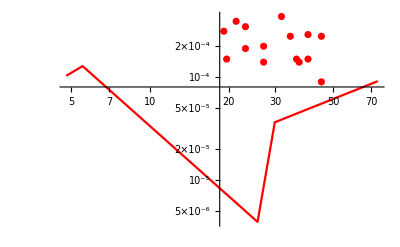

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca, dataT1C10Delay}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
If[exportYes==1,
Export["plot delay C10 data.txt",Transpose[{dataT1C10Ca, dataT1C10Delay}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]],simParamMedianC10[[simParam,All]],simParamQuantile2C10[[simParam,All]]}];
Export["plot delay C10 fit - quantiles and median.txt",toExport,"Table"];
];
```

### D

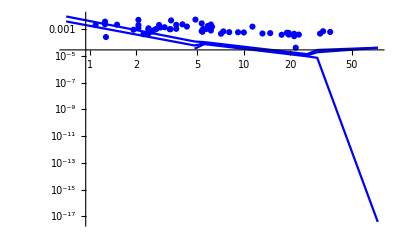

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT1DCa, dataT1DDelay}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianD[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
If[exportYes==1,
Export["plot delay D data.txt",Transpose[{dataT1DCa, dataT1DDelay}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]],simParamMedianD[[simParam,All]],simParamQuantile2D[[simParam,All]]}];
Export["plot delay D fit - quantiles and median.txt",toExport,"Table"];
];
```

### C5 and C10 and D

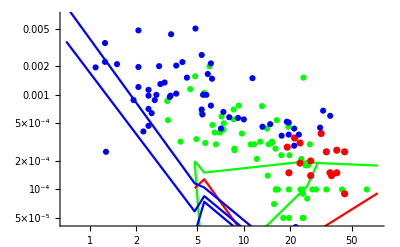

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{-10,-5}]
```

```mathematica
Show[gr1a,gr1b,gr1c,PlotRange->All];
```

## amp (merge of mono amp and bi amp)

```mathematica
simParam=13;
```

### C5

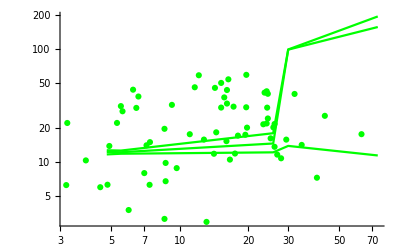

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca,dataT1C5Amplitude}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
```

### C10

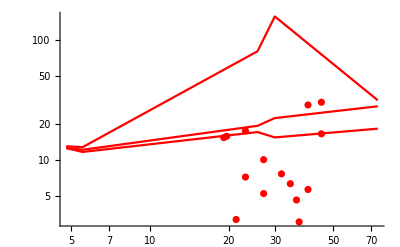

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca, dataT1C10Amplitude}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
```

### D

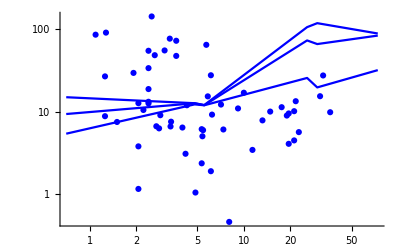

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT1DCa, dataT1DAmplitude}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianD[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
```

### C5 and C10 and D

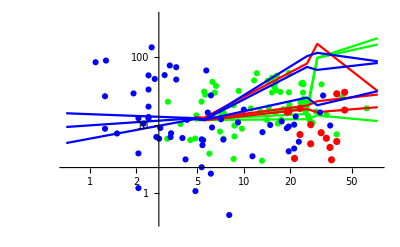

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{-1,6} ]
```

## release rate 1/tau2 of bi fits (if bi is justified)

```mathematica
simParam=16;
```

### C5

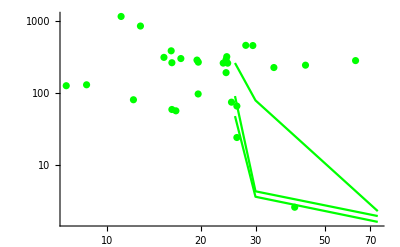

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT2C5Ca, dataT2C5RelRate}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau2 C5 data.txt",Transpose[{dataT2C5Ca, dataT2C5RelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]],simParamMedianC5[[simParam,All]],simParamQuantile2C5[[simParam,All]]}];
Export["plot InvTau2 C5 fit - quantiles and median.txt",toExport,"Table"];
];
```

### C10

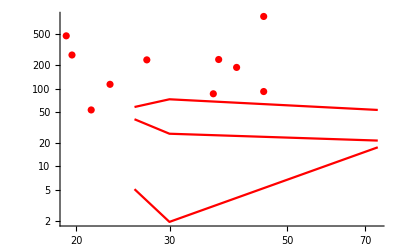

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT2C10Ca, dataT2C10RelRate}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau2 C10 data.txt",Transpose[{dataT2C10Ca, dataT2C10RelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]],simParamMedianC10[[simParam,All]],simParamQuantile2C10[[simParam,All]]}];
Export["plot InvTau2 C10 fit - quantiles and median.txt",toExport,"Table"];
];
```

### D

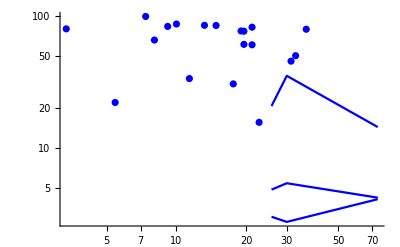

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT2DCa, dataT2DRelRate}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianD[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2D[[simParam,All]]}],PlotStyle ->{ colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
If[exportYes==1,
Export["plot InvTau2 D data.txt",Transpose[{dataT2DCa, dataT2DRelRate}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]],simParamMedianD[[simParam,All]],simParamQuantile2D[[simParam,All]]}];
Export["plot InvTau2 D fit - quantiles and median.txt",toExport,"Table"];
];
```

### C5 and C10 and D

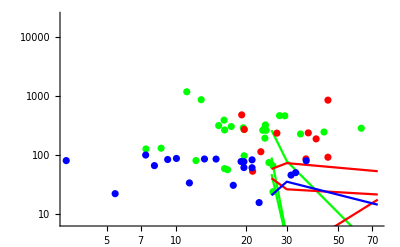

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{All,{2,10}}]
```

```mathematica
Show[gr1a,gr1b,gr1c,PlotRange->All];
```

## amp1 of bi fits (if bi is justified)

```mathematica
simParam=14;
```

### C5

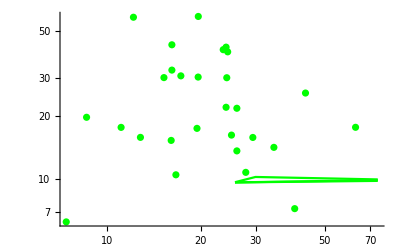

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT2C5Ca, dataT2C5Amplitude1}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{ colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->All ]
```

### C10

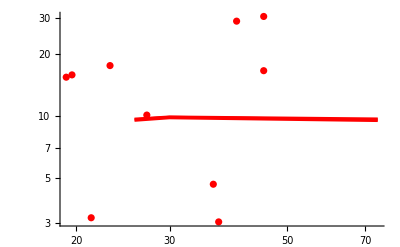

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT2C10Ca, dataT2C10Amplitude1}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianC10[[simParam,All]]}],PlotStyle ->{ colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
```

### D

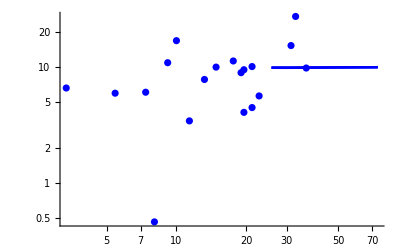

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT2DCa, dataT2DAmplitude1}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamMedianD[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile1D[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamQuantile2D[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
```

### C5 and C10 and D

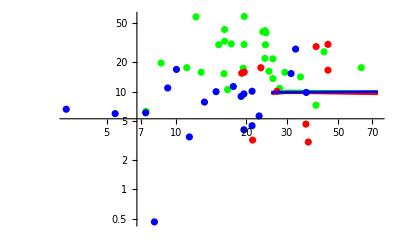

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->All]
Show[gr1a,gr1b,gr1c,PlotRange->All];
```

## chi2 mono/bi ratio

```mathematica
simParam=6;
```

### C5

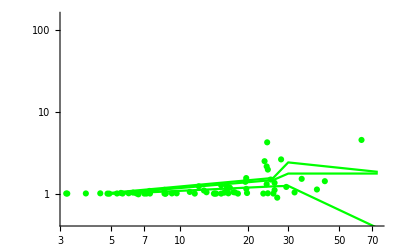

```mathematica
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca,dataT1C5ChiRatio}],PlotStyle->{colorA}];
gr2a=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr3a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
gr4a=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C5[[simParam,All]]}],PlotStyle ->{colorA},Joined->True, PlotRange->All];
Show[gr1a,gr2a,gr3a,gr4a,PlotRange->{All,{-0.8,5}} ]
If[exportYes==1,
Export["plot chi2Ratio C5 data.txt",Transpose[{dataT1C5Ca, dataT1C5ChiRatio}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C5[[simParam,All]],simParamMedianC5[[simParam,All]],simParamQuantile2C5[[simParam,All]]}];
Export["plot chi2Ratio C5 fit - quantiles and median.txt",toExport,"Table"];
];
```

### C10

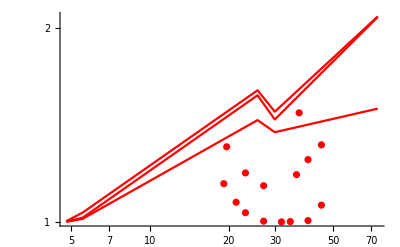

```mathematica
gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca,dataT1C10ChiRatio}],PlotStyle->{colorB}];
gr2b=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianC10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
gr3b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
gr4b=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2C10[[simParam,All]]}],PlotStyle ->{colorB},Joined->True, PlotRange->All];
Show[gr1b,gr2b,gr3b,gr4b,PlotRange->All ]
If[exportYes==1,
Export["plot chi2Ratio C10 data.txt",Transpose[{dataT1C10Ca, dataT1C10ChiRatio}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1C10[[simParam,All]],simParamMedianC10[[simParam,All]],simParamQuantile2C10[[simParam,All]]}];
Export["plot chi2Ratio C10 fit - quantiles and median.txt",toExport,"Table"];
];
```

### D

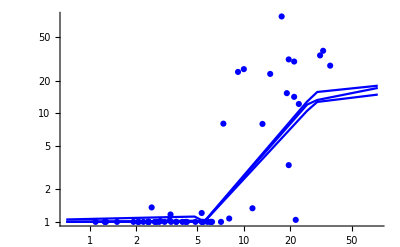

```mathematica
gr1c=ListLogLogPlot[Transpose[{dataT1DCa,dataT1DChiRatio}],PlotStyle->{colorC}];
gr2c=ListLogLogPlot[Transpose[{caFact simCaList,simParamMedianD[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
gr3c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
gr4c=ListLogLogPlot[Transpose[{caFact simCaList,simParamQuantile2D[[simParam,All]]}],PlotStyle ->{colorC},Joined->True, PlotRange->All];
Show[gr1c,gr2c,gr3c,gr4c,PlotRange->All ]
If[exportYes==1,
Export["plot chi2Ratio D data.txt",Transpose[{dataT1DCa, dataT1DChiRatio}],"Table"];
toExport=Transpose[{caFact simCaList,simParamQuantile1D[[simParam,All]],simParamMedianD[[simParam,All]],simParamQuantile2D[[simParam,All]]}];
Export["plot chi2Ratio D fit - quantiles and median.txt",toExport,"Table"];
];
```

### C5 and C10 and D

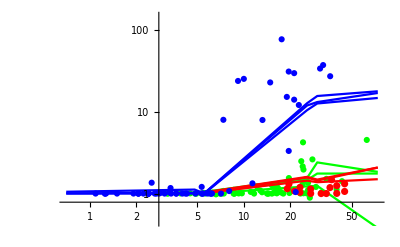

```mathematica
Show[gr1a,gr2a,gr3a,gr4a,gr1b,gr2b,gr3b,gr4b,gr1c,gr2c,gr3c,gr4c,PlotRange->{All,{-0.8,5}}]
Show[gr1a,gr1b,gr1c,PlotRange->All];
```

## Nv

time for Nv (ms) = 0.1

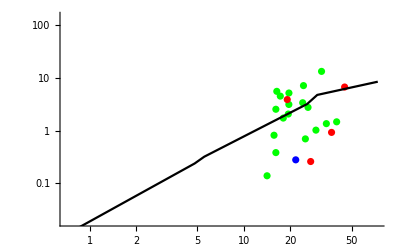

time for Nv (ms) = 0.2

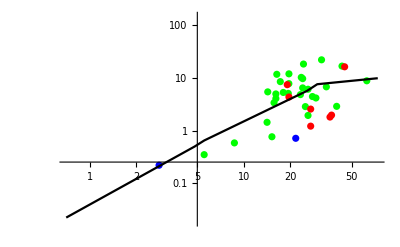

time for Nv (ms) = 1.

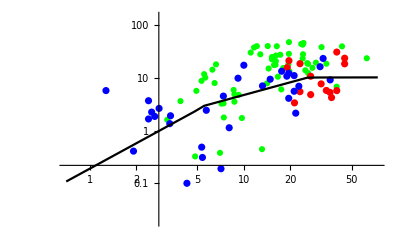

time for Nv (ms) = 5.

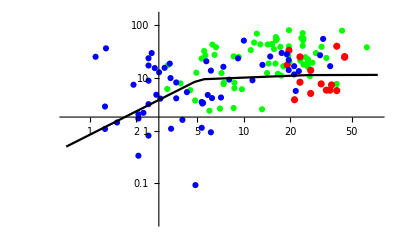

time for Nv (ms) = 10.

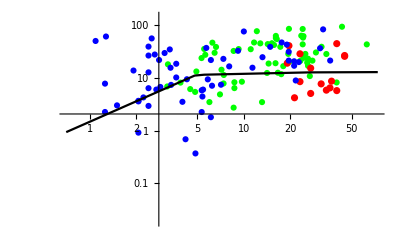

time for Nv (ms) = 100.

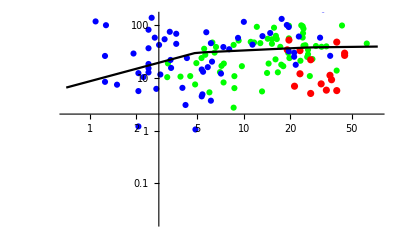

time for Nv (ms) = 400.

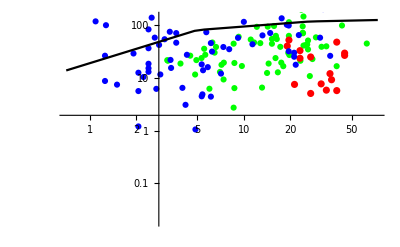

```mathematica
For[NvCount=1,NvCount≤7,NvCount+=1,
Print[" time for Nv (ms) = ",1000*timeOfNv[[NvCount]]];
gr1a=ListLogLogPlot[Transpose[{dataT1C5Ca,dataT1C5Nv[[NvCount]]}],PlotStyle->{colorA}];gr1b=ListLogLogPlot[Transpose[{dataT1C10Ca,dataT1C10Nv[[NvCount]]}],PlotStyle->{colorB}];gr1c=ListLogLogPlot[Transpose[{dataT1DCa,dataT1DNv[[NvCount]]}],PlotStyle->{colorC}];gr2=ListLogLogPlot[Transpose[{caFact simCaList,rrp simParamNv[[NvCount,All]]}],PlotStyle ->{ Black},Joined->True, PlotRange->All];
Show[gr1a,gr1b,gr1c,gr2,PlotRange->{All,{-4,5}} ]//Print;
];
```

## sustained release 10 to 100 ms

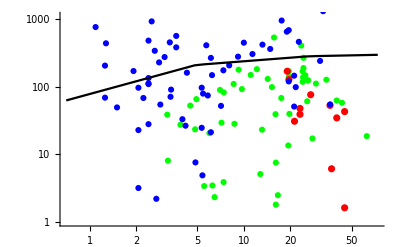

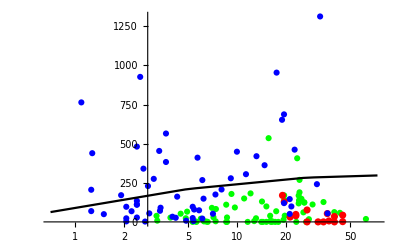

```mathematica
ttt1=Transpose[{dataT1C5Ca,(dataT1C5Nv[[6]]-dataT1C5Nv[[5]])/0.09}];
ttt2=Transpose[{dataT1C10Ca,(dataT1C10Nv[[6]]-dataT1C10Nv[[5]])/0.09}];
ttt3=Transpose[{dataT1DCa,(dataT1DNv[[6]]-dataT1DNv[[5]])/0.09}];
ttt4=Transpose[{caFact simCaList,rrp (simParamNv[[6,All]]-simParamNv[[5,All]])/0.09}];

gr1a=ListLogLogPlot[ttt1,PlotStyle->{colorA}];gr1b=ListLogLogPlot[ttt2,PlotStyle->{colorB}];gr1c=ListLogLogPlot[ttt3,PlotStyle->{colorC}];gr2=ListLogLogPlot[ttt4,PlotStyle ->{ Black},Joined->True, PlotRange->All];
Show[gr1a,gr1b,gr1c,gr2,PlotRange->{All,{0,7}} ]//Print;

gr1a=ListLogLinearPlot[ttt1,PlotStyle->{colorA}];gr1b=ListLogLinearPlot[ttt2,PlotStyle->{colorB}];gr1c=ListLogLinearPlot[ttt3,PlotStyle->{colorC}];gr2=ListLogLinearPlot[ttt4,PlotStyle ->{ Black},Joined->True, PlotRange->All];
Show[gr1a,gr1b,gr1c,gr2,PlotRange->{All,All} ]//Print;
```

```mathematica
If[exportYes==1,
Export["plot sustained release Cm5 data.txt",ttt1,"Table"];
Export["plot sustained release Cm10 data.txt",ttt2,"Table"];
Export["plot sustained release D data.txt",ttt3,"Table"];
Export["plot sustained release sim.txt",ttt4,"Table"]
];
```

## Export Nv

```mathematica
If[exportYes==1,
Export["Nv export Ca,0.0001,0.0002,0.001,0.005,0.01,0.1,0.4.txt",Transpose[Prepend[simParamNv,caFact simCaList]],"Table"];
];
```

## Print some values

### C5

```mathematica
Transpose[simParamMedianC5]//TableForm
Transpose[simParamQuantile1C5]//TableForm
Transpose[simParamQuantile2C5]//TableForm
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0.558169 | 0.000196264 | 1.22645 | 244.494 | 1.00456 | 0.0002 | 1.55268 | 0.840996 | 372.818 | 15.8651 | 0.000196264 | 1.22645 | Median[{}] | 244.494 | Median[{}]
0 | 0.442238 | 9.28401×10^-6 | 1.21939 | 320.467 | 1.01348 | -0.00013109 | 0.912317 | 3.67211 | 196.729 | 75.5101 | 9.28401×10^-6 | 1.21939 | Median[{}] | 320.467 | Median[{}]
0 | 0.691305 | -7.7468×10^-6 | 1.15806 | 2638.91 | 1.46508 | 0.000108196 | 1.45623 | 0.96807 | 8872.8 | 90.6305 | 0.000108196 | 1.45623 | 0.96807 | 8872.8 | 90.6305
0 | 0.82562 | -7.25179×10^-6 | 1.14792 | 4022.54 | 1.75847 | 0.00018539 | 9.81436 | 0.969461 | 106992. | 4.23879 | 0.00018539 | 9.81436 | 0.969461 | 106992. | 4.23879
0 | 0.857236 | -1.32507×10^-8 | 1.143 | 15481. | 1.75957 | 0.00017904 | 15.5432 | 0.998211 | 608202. | 2.23977 | -8.5×10^-18 | 15.5432 | 0.990382 | 150053. | 1.91226

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0.535 | 0.000108148 | 1.16632 | 223.507 | 0.996897 | 0.0002 | 1.298 | 0.0598399 | 255.852 | 4.20069 | 0.000108148 | 1.16632 | Quantile[{},0.25] | 223.507 | Quantile[{},0.25]
0 | 0.419633 | -0.00012179 | 1.18265 | 265.976 | 0.997228 | -0.00015499 | 0.436132 | 1.16961 | 151.55 | 1.45021 | -0.00012179 | 1.18265 | Quantile[{},0.25] | 265.976 | Quantile[{},0.25]
0 | 0.649345 | -0.0000558478 | 1.14232 | 2156.84 | 1.22491 | -1.09854×10^-18 | 1.21659 | 0.964012 | 4375.48 | 47.6165 | -1.09854×10^-18 | 1.21659 | 0.964012 | 4375.48 | 47.6165
0 | 0.786886 | -0.0000125089 | 1.12785 | 3704.23 | 1.24222 | -1.03232×10^-15 | 1.38662 | 0.968329 | 6213.03 | 3.55863 | -1.03232×10^-15 | 1.38662 | 0.968329 | 6213.03 | 3.55863
0 | 0.795738 | -4.77651×10^-6 | 1.14183 | 5747.24 | 0.37743 | -5.05312×10^-7 | 10.783 | 0.982552 | 150053. | 1.58474 | -5.05312×10^-7 | 1.14183 | 0.982552 | 5747.24 | 1.58474

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 0.577463 | 0.0002 | 1.26918 | 272.268 | 1.00805 | 0.00020429 | 7.96209 | 1.15495 | 2520.94 | 207.015 | 0.0002 | 1.26918 | Quantile[{},0.75] | 272.268 | Quantile[{},0.75]
0 | 0.599915 | 0.000150731 | 1.26134 | 346.413 | 1.04856 | 0.000204061 | 3.91975 | 3.91523 | 342.954 | 136.521 | 0.000150731 | 1.26134 | Quantile[{},0.75] | 346.413 | Quantile[{},0.75]
0 | 0.815492 | -1.3188×10^-6 | 1.15818 | 3116.89 | 1.55272 | 0.000198536 | 1.79492 | 0.968375 | 339321. | 262.587 | 0.000198536 | 1.79492 | 0.968375 | 339321. | 262.587
0 | 0.852301 | 1.51466×10^-18 | 1.16416 | 6069.04 | 2.40935 | 0.000190291 | 9.84813 | 1.02517 | 117163. | 78.8999 | 0.000190291 | 9.84813 | 1.02517 | 117163. | 78.8999
0 | 0.928748 | -8.5×10^-18 | 1.14538 | 4.9648×10^6 | 1.84609 | 0.000595672 | 19.2662 | 1.01854 | 1.61639×10^6 | 2.70803 | 0.00017904 | 19.2662 | 0.998211 | 1.61639×10^6 | 2.23977

### C10

```mathematica
Transpose[simParamMedianC10]//TableForm
Transpose[simParamQuantile1C10]//TableForm
Transpose[simParamQuantile2C10]//TableForm
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1.11476 | 0.0000484428 | 1.27367 | 214.143 | 1.00129 | 0.0000261636 | 1.06558 | 1.30946 | 214.143 | 65.6763 | 0.0000484428 | 1.27367 | Median[{}] | 214.143 | Median[{}]
0 | 1.02481 | -7.15539×10^-6 | 1.22143 | 308.766 | 1.01479 | -0.0000569535 | 0.455629 | 2.90733 | 184.113 | 77.172 | -7.15539×10^-6 | 1.22143 | Median[{}] | 308.766 | Median[{}]
0 | 1.69268 | -0.000129442 | 1.17196 | 1792.17 | 1.57304 | -0.0000213642 | 1.93704 | 0.962159 | 4175.53 | 40.3761 | -0.0000213642 | 1.93704 | 0.962159 | 4175.53 | 40.3761
0 | 1.79081 | -3.41449×10^-6 | 1.14068 | 4857.44 | 1.4426 | -7.85951×10^-18 | 2.24612 | 0.989544 | 8308.08 | 26.2994 | -7.85951×10^-18 | 2.24612 | 0.989544 | 8308.08 | 26.2994
0 | 2.2687 | -0.000117644 | 1.16258 | 3994.8 | 2.08245 | 0.0000134971 | 2.82013 | 0.960032 | 22543.4 | 21.4762 | 0.0000134971 | 2.82013 | 0.960032 | 22543.4 | 21.4762

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1.05691 | 0.0000261636 | 1.261 | 200.008 | 1. | 0.0000239968 | 0.777713 | 0.817379 | 135.753 | 15.5263 | 0.0000261636 | 1.261 | Quantile[{},0.25] | 200.008 | Quantile[{},0.25]
0 | 0.951601 | -0.0000134287 | 1.1716 | 269.382 | 1.01083 | -0.0000854457 | 0.405774 | 0.398878 | 152.2 | 74.6738 | -0.0000134287 | 1.1716 | Quantile[{},0.25] | 269.382 | Quantile[{},0.25]
0 | 1.58283 | -0.000130109 | 1.16647 | 1587.15 | 1.43932 | -0.000049544 | 1.71711 | 0.947993 | 3820.09 | 5.09497 | -0.000049544 | 1.71711 | 0.947993 | 3820.09 | 5.09497
0 | 1.77225 | -0.000063172 | 1.13967 | 3033.16 | 1.37836 | -3.92754×10^-6 | 1.54891 | 0.97525 | 7758.78 | 1.9334 | -3.92754×10^-6 | 1.54891 | 0.97525 | 7758.78 | 1.9334
0 | 1.93837 | -0.0002 | 1.15261 | 2109.71 | 1.49977 | -0.000108107 | 1.83289 | 0.94555 | 5924.98 | 17.5894 | -0.000108107 | 1.83289 | 0.94555 | 5924.98 | 17.5894

|  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1.20884 | 0.000102995 | 1.30731 | 221.396 | 1.00234 | 0.0001 | 1.27367 | 2.85899 | 214.983 | 214.143 | 0.000102995 | 1.30731 | Quantile[{},0.75] | 221.396 | Quantile[{},0.75]
0 | 1.28054 | 0.00012816 | 1.28444 | 328.931 | 1.03365 | 0.0003 | 1.39414 | 3.66401 | 956.579 | 164.899 | 0.00012816 | 1.28444 | Quantile[{},0.75] | 328.931 | Quantile[{},0.75]
0 | 1.71333 | -0.000105122 | 1.17977 | 1803.73 | 1.60145 | 3.89543×10^-6 | 8.12569 | 0.969265 | 4671.49 | 58.0079 | 3.89543×10^-6 | 8.12569 | 0.969265 | 4671.49 | 58.0079
0 | 1.91997 | -4.23888×10^-18 | 1.17302 | 5613.36 | 1.48355 | 0.0000363526 | 15.8631 | 0.992818 | 11005. | 72.9131 | 0.0000363526 | 15.8631 | 0.992818 | 11005. | 72.9131
0 | 2.45429 | -2.17565×10^-18 | 1.17529 | 10044.1 | 2.08614 | 0.0000913627 | 3.1629 | 0.970963 | 334803. | 53.1737 | 0.0000913627 | 3.1629 | 0.970963 | 334803. | 53.1737

### D

```mathematica
Transpose[simParamMedianD]//TableForm
Transpose[simParamQuantile1D]//TableForm
Transpose[simParamQuantile2D]//TableForm
```

0 | 1.07522 | 0.00366323 | 0.933623 | 12.2735 | 1.00524 | -0.003 | 4.77001 | 0.0630768 | 42.1674 | 1.40196 | 0.00366323 | 0.933623 | Median[{}] | 12.2735 | Median[{}]
0 | 0.0470871 | 0.0000586294 | 1.2585 | 220.807 | 1.02416 | 0.0000301442 | 0.532762 | 1.99791 | 163.241 | 41.1778 | 0.0000586294 | 1.2585 | Median[{}] | 220.807 | Median[{}]
0 | 0.0445167 | 0.0000850033 | 1.19294 | 321.725 | 1.00325 | 0.0000802138 | 0.766294 | 1.23061 | 311.024 | 5.50224 | 0.0000850033 | 1.19294 | Median[{}] | 321.725 | Median[{}]
0 | 0.530804 | -0.0000355205 | 1.15689 | 2444.95 | 12.023 | 0.0000107076 | 7.22358 | 0.987617 | 4460.07 | 4.82833 | 0.0000107076 | 7.22358 | 0.987617 | 4460.07 | 4.82833
0 | 0.611601 | -0.0000171127 | 1.1509 | 3815.31 | 13.2444 | 0.000018316 | 6.53023 | 0.990581 | 7625.26 | 5.40063 | 0.000018316 | 6.53023 | 0.990581 | 7625.26 | 5.40063
0 | 0.729864 | 8.15023×10^-18 | 1.15388 | 10355.7 | 17.105 | 0.0000391999 | 8.27077 | 0.997597 | 26476.6 | 4.19588 | 0.0000391999 | 8.27077 | 0.997597 | 26476.6 | 4.19588

0 | 1.03411 | -0.00337928 | 0.54024 | 5.75488 | 1.0002 | -0.028 | 4.17007 | -4.83606 | 6.77846 | 1.35399 | -0.00337928 | 0.54024 | Quantile[{},0.25] | 5.75488 | Quantile[{},0.25]
0 | 0.0454326 | 0.0000336663 | 1.2204 | 220.377 | 1.00026 | 0.0000272162 | 0.508027 | 1.3005 | 145.566 | 13.4708 | 0.0000336663 | 1.2204 | Quantile[{},0.25] | 220.377 | Quantile[{},0.25]
0 | 0.0390724 | 0.0000740578 | 1.19059 | 319.637 | 1.00155 | 0.0000700207 | 0.694394 | 1.21961 | 302.627 | 5.38866 | 0.0000740578 | 1.19059 | Quantile[{},0.25] | 319.637 | Quantile[{},0.25]
0 | 0.507636 | -0.0000453135 | 1.15462 | 2250.41 | 10.5369 | 9.09647×10^-6 | 2.54573 | 0.983877 | 4388.06 | 3.00548 | 9.09647×10^-6 | 2.54573 | 0.983877 | 4388.06 | 3.00548
0 | 0.577697 | -0.0000285742 | 1.14859 | 3546.18 | 12.7172 | 6.97549×10^-6 | 1.95636 | 0.983078 | 7311.54 | 2.74623 | 6.97549×10^-6 | 1.95636 | 0.983078 | 7311.54 | 2.74623
0 | 0.703231 | -7.14717×10^-7 | 1.15262 | 9383.21 | 14.8626 | 3.86005×10^-18 | 3.16375 | 0.993896 | 20395.4 | 4.08594 | 3.86005×10^-18 | 3.16375 | 0.993896 | 20395.4 | 4.08594

0 | 1.12516 | 0.00862974 | 1.48961 | 31.2373 | 1.05217 | 0.0110829 | 9.46705 | 0.185328 | 119.617 | 2.33932 | 0.00862974 | 1.48961 | Quantile[{},0.75] | 31.2373 | Quantile[{},0.75]
0 | 0.0558425 | 0.00011618 | 1.26081 | 241.017 | 1.11916 | 0.0000628942 | 1.06289 | 3.06861 | 214.599 | 67.5226 | 0.00011618 | 1.26081 | Quantile[{},0.75] | 241.017 | Quantile[{},0.75]
0 | 0.0464539 | 0.00010479 | 1.19823 | 325.886 | 1.00597 | 0.0000949808 | 1.14423 | 1.32563 | 314.473 | 108.489 | 0.00010479 | 1.19823 | Quantile[{},0.75] | 325.886 | Quantile[{},0.75]
0 | 0.543468 | -0.00003188 | 1.15839 | 2488.35 | 12.8128 | 0.0000132203 | 10.4532 | 0.994364 | 4769.66 | 20.8382 | 0.0000132203 | 10.4532 | 0.994364 | 4769.66 | 20.8382
0 | 0.614661 | -0.0000117758 | 1.15154 | 4248.87 | 15.7052 | 0.0000270937 | 11.6767 | 0.991481 | 8697.46 | 35.3582 | 0.0000270937 | 11.6767 | 0.991481 | 8697.46 | 35.3582
0 | 0.784491 | 1.52571×10^-17 | 1.15582 | 11243.3 | 17.9428 | 0.0000397785 | 8.76096 | 0.999729 | 28157.8 | 14.4239 | 0.0000397785 | 8.76096 | 0.999729 | 28157.8 | 14.4239

### Nv

```mathematica
Transpose[simParamNv]//TableForm
```

0.00105711 | 0.00221298 | 0.0107502 | 0.0495193 | 0.093503 | 0.658054 | 1.39403
0.0236597 | 0.0497429 | 0.230838 | 0.844272 | 1.11259 | 2.97902 | 7.90239
0.0318492 | 0.0648821 | 0.296443 | 0.950337 | 1.15738 | 3.09028 | 8.36165
0.319936 | 0.570673 | 1.01314 | 1.13623 | 1.27814 | 3.8082 | 11.8076
0.477046 | 0.762426 | 1.02364 | 1.13927 | 1.28265 | 3.84227 | 11.9911
0.851423 | 0.991712 | 1.02808 | 1.14729 | 1.29626 | 3.96853 | 12.704

# EPSC with different caRest

## Interpolate

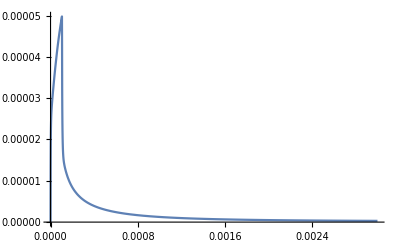

```mathematica
locaCa=Transpose[{dataLocalCaTime,dataLocalCa}];
locaCaWithoutdublictes=Mean/@GatherBy[locaCa,First];
interpolFunc=Interpolation[locaCaWithoutdublictes,InterpolationOrder->1];
caFunc[t_]:=interpolFunc[t];
Plot[caFunc[t],{t,0.00,0.003},PlotRange->All]
```

## NDSolve

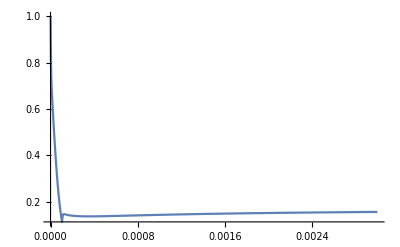

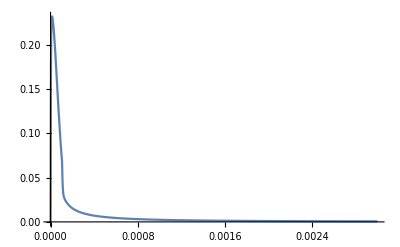

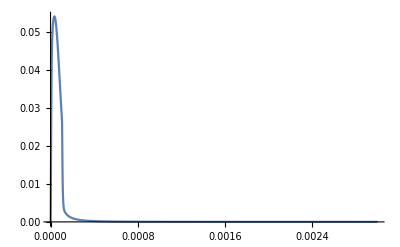

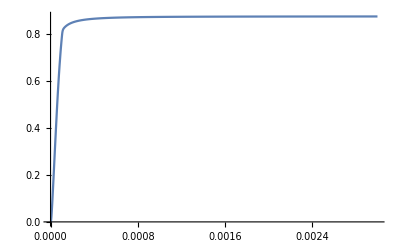

```mathematica
timeStartForPLot=0.0;
timeEndForPLot=0.003;
myNDSolveResults=NDSolve[eq,{ss1,ss2,ss3,ss4},{t,0,0.003}];
Plot[(ss1[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss2[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss3[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss4[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
```

## different caRest

```mathematica
caRestLow=30*^-9;
caRestHigh=180*^-9;
```

## Low Ca

## Initial occupancy

```mathematica
(*calualte initial equilibrium occupancy*)
caFunc[t_]:=caRestLow;
kprimScheme
kunprimScheme
ss0Initial=kprimScheme/kunprimScheme
```

1.04335

3.65793

0.28523

## Diff eq.

```mathematica
Clear[caFunc,eq];(*Clear is needed if the cell is exectued for a 2nd time when caFunc is already set to a value or an Interpolationfunction*)
caFunc[t_]:=interpolFunc[t];
ss[t_]={ss1[t],ss2[t],ss3[t],ss4[t]};
eq={ss'[t]==(mat/.repl).ss[t],
ss[0]=={ss0Initial,0,0,0}};
```

## NDSolve

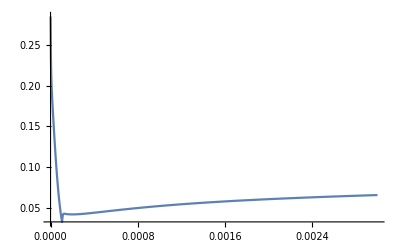

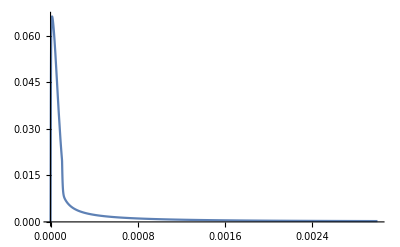

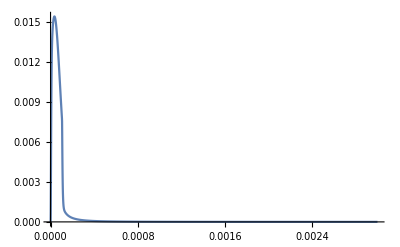

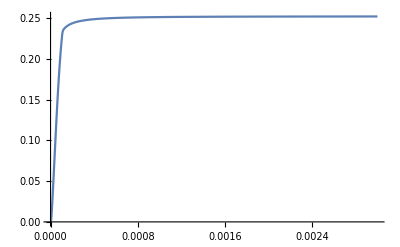

```mathematica
myNDSolveResults=NDSolve[eq,{ss1,ss2,ss3,ss4},{t,0,0.003}];
Plot[(ss1[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss2[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss3[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss4[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
```

## Plot EPSC

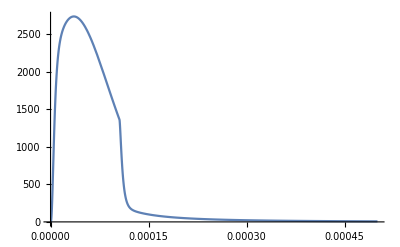

```mathematica
epscLowCa=D[(ss4[t]/.myNDSolveResults),t];
Plot[(ss4[t]/.myNDSolveResults),{t,0,2*^-3},PlotRange->All];
Plot[epscLowCa,{t,0,0.5*^-3},PlotRange->All]
```

## High Ca

## Initial occupancy

```mathematica
(*calualte initial equilibrium occupancy*)
caFunc[t_]:=caRestHigh;
kprimScheme
kunprimScheme
ss0Initial=kprimScheme/kunprimScheme
```

3.07706

3.65793

0.841205

## Diff eq.

```mathematica
Clear[caFunc,eq];(*Clear is needed if the cell is exectued for a 2nd time when caFunc is already set to a value or an Interpolationfunction*)
caFunc[t_]:=interpolFunc[t];
ss[t_]={ss1[t],ss2[t],ss3[t],ss4[t]};
eq={ss'[t]==(mat/.repl).ss[t],
ss[0]=={ss0Initial,0,0,0}};
```

## NDSolve

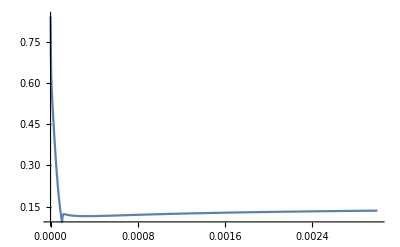

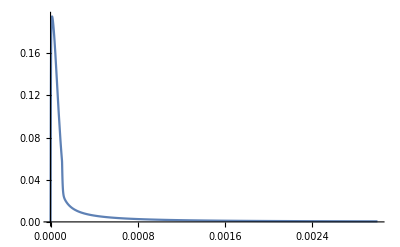

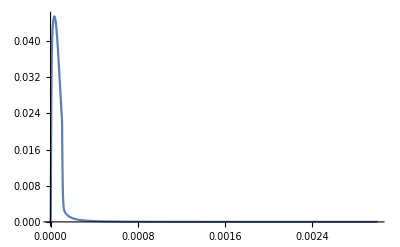

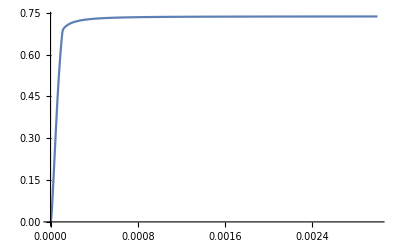

```mathematica
myNDSolveResults=NDSolve[eq,{ss1,ss2,ss3,ss4},{t,0,0.003}];
Plot[(ss1[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss2[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss3[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
Plot[(ss4[t]/.myNDSolveResults),{t,timeStartForPLot,timeEndForPLot},PlotRange->All]
```

## Plot EPSC

```mathematica
epscHighCa=D[(ss4[t]/.myNDSolveResults),t];
Plot[(ss4[t]/.myNDSolveResults),{t,0,2*^-3},PlotRange->All];
Plot[epscLowCa,{t,0,0.5*^-3},PlotRange->All]
```

-Graphics-

## Compare

## Plot both release rates

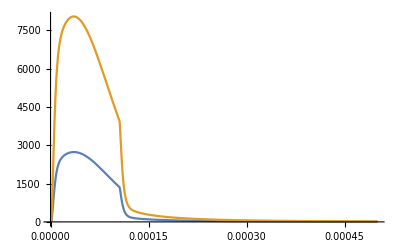

```mathematica
Plot[{epscLowCa,epscHighCa},{t,0,0.5*^-3},PlotRange->All]
```

## Convolution RelRate => EPSC

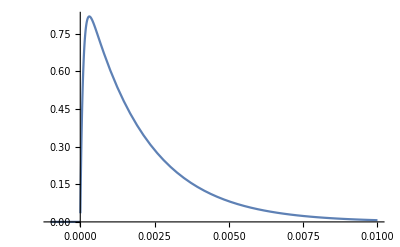

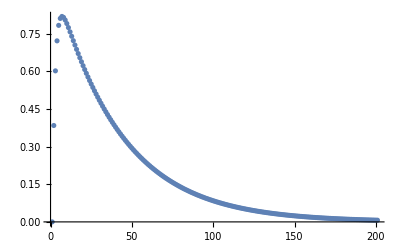

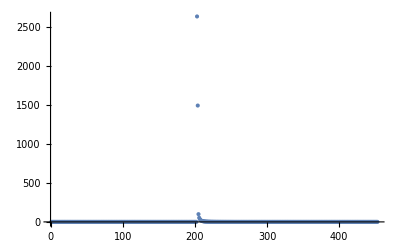

```mathematica
miniKernel[t_]:=If[t≤0,0,(1-Exp[-t/0.0001])*Exp[-t/0.002]];
Plot[miniKernel[t],{t,-.001,.01}]
dtForConvolve=0.00005;
tEndConv=0.01;
miniKernelList=Table[miniKernel[t],{t,0.0,tEndConv,dtForConvolve}];
epscHighCaList={Table[0,{t,0,tEndConv,dtForConvolve}],Table[epscHighCa,{t,0.0,0.0025,dtForConvolve}],Table[0,{t,0,tEndConv,dtForConvolve}]}//Flatten;epscLowCaList={Table[0,{t,0,tEndConv,dtForConvolve}],Table[epscLowCa,{t,0.0,0.0025,dtForConvolve}],Table[0,{t,0,tEndConv,dtForConvolve}]}//Flatten;
ListPlot[miniKernelList]
ListPlot[epscLowCaList,PlotRange->All]
```

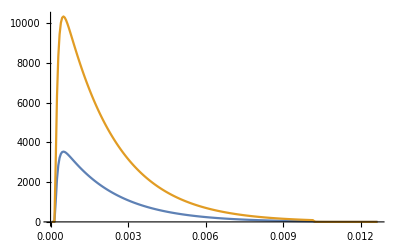

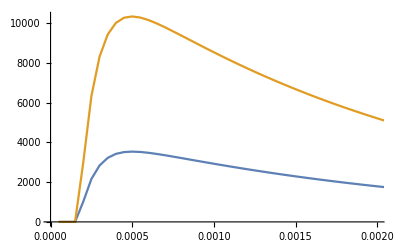

3532.14

10325.2

maxHigh/maxLow = 2.92322

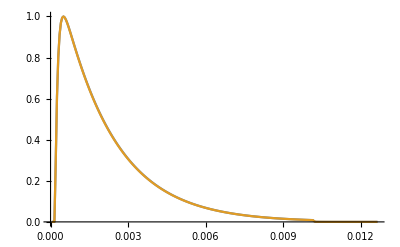

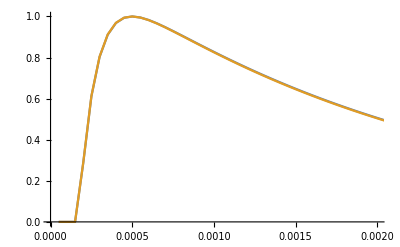

```mathematica
epscLowCaCurrentList=ListConvolve[miniKernelList,epscLowCaList];
epscHighCaCurrentList=ListConvolve[miniKernelList,epscHighCaList];
timeConv=Table[t*dtForConvolve,{t,Length[epscLowCaCurrentList]}];
ListPlot[{Transpose[{timeConv,epscLowCaCurrentList}],Transpose[{timeConv,epscHighCaCurrentList}]},Joined->True,PlotRange->All]
ListPlot[{Transpose[{timeConv,epscLowCaCurrentList}],Transpose[{timeConv,epscHighCaCurrentList}]},Joined->True,PlotRange->{{0,0.002},All}]
maxLow=Max[epscLowCaCurrentList]
maxHigh=Max[epscHighCaCurrentList]
Print["maxHigh/maxLow = ",maxHigh/maxLow];
ListPlot[{Transpose[{timeConv,(1/maxLow)*epscLowCaCurrentList}],Transpose[{timeConv,(1/maxHigh)*epscHighCaCurrentList}]},Joined->True,PlotRange->All]
ListPlot[{Transpose[{timeConv,(1/maxLow)*epscLowCaCurrentList}],Transpose[{timeConv,(1/maxHigh)*epscHighCaCurrentList}]},Joined->True,PlotRange->{{0,0.002},All}]
If[exportYes==1,
toExport=Transpose[{timeConv,epscLowCaCurrentList,epscHighCaCurrentList,(1/maxLow)*epscLowCaCurrentList,(1/maxHigh)*epscHighCaCurrentList}];
Export["plot EPSC - low and high - abs and norm.txt",toExport,"Table"];
];
```

# Timing

```mathematica
timeEnd=AbsoluteTime[];
(timeEnd-timeStart )/60.(* time of calculation in min *)
```

0.224448